```mathematica
DSolve[D[D[u[t],t],t]+u[t]==f Sin[ω t]Cos[t+ϕ]+2 f ω Cos[ω t]Sin[t+ϕ],u[t],{t,0,100}]
```

{{u[t]→1/(2 ω (-4+ω^2))(2 ω (-4+ω^2) C[1] Cos[t]+2 ω (-4+ω^2) C[2] Sin[t]+f ((2-3 ω-2 ω^2) Sin[t+ϕ-t ω]+(2+3 ω-2 ω^2) Sin[t+ϕ+t ω]))}}

```mathematica
Simplify[%]
```

{{u[t]→1/(2 ω (-4+ω^2))(2 ω (-4+ω^2) C[1] Cos[t]+2 ω (-4+ω^2) C[2] Sin[t]+f ((2-3 ω-2 ω^2) Sin[t+ϕ-t ω]+(2+3 ω-2 ω^2) Sin[t+ϕ+t ω]))}}

```mathematica
Expand[%]
```

{{u[t]→-(4 C[1] Cos[t])/(-4+ω^2)+(ω^2 C[1] Cos[t])/(-4+ω^2)-(4 C[2] Sin[t])/(-4+ω^2)+(ω^2 C[2] Sin[t])/(-4+ω^2)-(3 f Sin[t+ϕ-t ω])/(2 (-4+ω^2))+(f Sin[t+ϕ-t ω])/(ω (-4+ω^2))-(f ω Sin[t+ϕ-t ω])/(-4+ω^2)+(3 f Sin[t+ϕ+t ω])/(2 (-4+ω^2))+(f Sin[t+ϕ+t ω])/(ω (-4+ω^2))-(f ω Sin[t+ϕ+t ω])/(-4+ω^2)}}

```mathematica
FullSimplify[%]
```

{{u[t]→1/(2 ω (-4+ω^2))((2+ω) (2 (-2+ω) ω (C[1] Cos[t]+C[2] Sin[t])+f (1-2 ω) Sin[t+ϕ-t ω])-f (-2+ω) (1+2 ω) Sin[t+ϕ+t ω])}}

```mathematica
(2-3 ω-2 ω^2)/(2 ω (-4+ω^2))
```

(2-3 ω-2 ω^2)/(2 ω (-4+ω^2))

```mathematica
FullSimplify[(2+3 ω-2 ω^2)/(2 ω (-4+ω^2))]
```

-(1+2 ω)/(4 ω+2 ω^2)

```mathematica
u0:=Subscript[f, 0] Cos[T+ϕ]
```

SetDelayed::write: Tag Times in (Cos[T+ϕ] f_0)[T,τ] is Protected.

$Failed

```mathematica
u1:= Subscript[f, 1][τ]Cos[T+ψ[τ]]+Subscript[f, 0]/(2ω)((1-2ω)/(ω-2)Sin[T+ϕ-ω T]-(1+2ω)/(ω+2)Sin[T+ϕ+ω T])
```

```mathematica
Simplify[-2 D[D[u1,T],τ]-Sin[ω T]D[D[u1,T],T]-2ω Cos[ω T]D[u1,T]]
```

-Sin[T ω] (((((-1+ω)^2 (-1+2 ω) Sin[T+ϕ-T ω])/(-2+ω)+((1+ω)^2 (1+2 ω) Sin[T+ϕ+T ω])/(2+ω)) f_0)/(2 ω)-Cos[T+ψ[τ]] f_1[τ])-2 ω Cos[T ω] (((((-1+ω) (-1+2 ω) Cos[T+ϕ-T ω])/(-2+ω)-((1+ω) (1+2 ω) Cos[T+ϕ+T ω])/(2+ω)) f_0)/(2 ω)-Sin[T+ψ[τ]] f_1[τ])+2 (Cos[T+ψ[τ]] f_1[τ] ψ'[τ]+Sin[T+ψ[τ]] f_1'[τ])

```mathematica
TrigReduce[%]
```

(-1/4 Cos[T+ϕ] f_0-1/4 ⅈ Sin[T+ϕ] f_0)/(2+ω)+(1/4 Cos[T+ϕ] f_0-1/4 ⅈ Sin[T+ϕ] f_0)/(-2+ω)+(-1/4 Cos[T+ϕ] f_0+1/4 ⅈ Sin[T+ϕ] f_0)/(2+ω)+(1/4 Cos[T+ϕ] f_0+1/4 ⅈ Sin[T+ϕ] f_0)/(-2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)-(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(-2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)-(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)+(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(-2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)+(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(2+ω)+(1/8 ω Cos[T+ϕ] f_0-1/8 ⅈ ω Sin[T+ϕ] f_0)/(-2+ω)+(1/8 ω Cos[T+ϕ] f_0-1/8 ⅈ ω Sin[T+ϕ] f_0)/(2+ω)+(1/8 ω Cos[T+ϕ] f_0+1/8 ⅈ ω Sin[T+ϕ] f_0)/(-2+ω)+(1/8 ω Cos[T+ϕ] f_0+1/8 ⅈ ω Sin[T+ϕ] f_0)/(2+ω)+(-1/4 ω^2 Cos[T+ϕ] f_0-1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(-2+ω)+(1/4 ω^2 Cos[T+ϕ] f_0-1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(2+ω)+(-1/4 ω^2 Cos[T+ϕ] f_0+1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(-2+ω)+(1/4 ω^2 Cos[T+ϕ] f_0+1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(2+ω)+(-3/4 Cos[T+ϕ-2 T ω] f_0-3/4 ⅈ Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(-3/4 Cos[T+ϕ-2 T ω] f_0+3/4 ⅈ Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+((Cos[T+ϕ-2 T ω] f_0)/(8 ω)-(ⅈ Sin[T+ϕ-2 T ω] f_0)/(8 ω))/(-2+ω)+((Cos[T+ϕ-2 T ω] f_0)/(8 ω)+(ⅈ Sin[T+ϕ-2 T ω] f_0)/(8 ω))/(-2+ω)+(11/8 ω Cos[T+ϕ-2 T ω] f_0-11/8 ⅈ ω Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(11/8 ω Cos[T+ϕ-2 T ω] f_0+11/8 ⅈ ω Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(-3/4 ω^2 Cos[T+ϕ-2 T ω] f_0-3/4 ⅈ ω^2 Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(-3/4 ω^2 Cos[T+ϕ-2 T ω] f_0+3/4 ⅈ ω^2 Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(3/4 Cos[T+ϕ+2 T ω] f_0-3/4 ⅈ Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(3/4 Cos[T+ϕ+2 T ω] f_0+3/4 ⅈ Sin[T+ϕ+2 T ω] f_0)/(2+ω)+((Cos[T+ϕ+2 T ω] f_0)/(8 ω)-(ⅈ Sin[T+ϕ+2 T ω] f_0)/(8 ω))/(2+ω)+((Cos[T+ϕ+2 T ω] f_0)/(8 ω)+(ⅈ Sin[T+ϕ+2 T ω] f_0)/(8 ω))/(2+ω)+(11/8 ω Cos[T+ϕ+2 T ω] f_0-11/8 ⅈ ω Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(11/8 ω Cos[T+ϕ+2 T ω] f_0+11/8 ⅈ ω Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(3/4 ω^2 Cos[T+ϕ+2 T ω] f_0-3/4 ⅈ ω^2 Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(3/4 ω^2 Cos[T+ϕ+2 T ω] f_0+3/4 ⅈ ω^2 Sin[T+ϕ+2 T ω] f_0)/(2+ω)-1/2 Sin[T-T ω+ψ[τ]] f_1[τ]+ω Sin[T-T ω+ψ[τ]] f_1[τ]+1/2 Sin[T+T ω+ψ[τ]] f_1[τ]+ω Sin[T+T ω+ψ[τ]] f_1[τ]+2 Cos[T+ψ[τ]] f_1[τ] ψ'[τ]+2 Sin[T+ψ[τ]] f_1'[τ]

```mathematica
TrigExpand[%]
```

(Cos[T] Cos[ϕ] f_0)/(2 (-2+ω))-(Cos[T] Cos[ϕ] f_0)/(4 (-2+ω) ω)+(ω Cos[T] Cos[ϕ] f_0)/(4 (-2+ω))-(ω^2 Cos[T] Cos[ϕ] f_0)/(2 (-2+ω))-(Cos[T] Cos[ϕ] f_0)/(2 (2+ω))-(Cos[T] Cos[ϕ] f_0)/(4 ω (2+ω))+(ω Cos[T] Cos[ϕ] f_0)/(4 (2+ω))+(ω^2 Cos[T] Cos[ϕ] f_0)/(2 (2+ω))-(3 Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(2 (-2+ω))+(Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(4 (-2+ω) ω)+(11 ω Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(4 (-2+ω))-(3 ω^2 Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(2 (-2+ω))+(3 Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(2 (2+ω))+(Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(4 ω (2+ω))+(11 ω Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(4 (2+ω))+(3 ω^2 Cos[T] Cos[ϕ] Cos[T ω]^2 f_0)/(2 (2+ω))-(Sin[T] Sin[ϕ] f_0)/(2 (-2+ω))+(Sin[T] Sin[ϕ] f_0)/(4 (-2+ω) ω)-(ω Sin[T] Sin[ϕ] f_0)/(4 (-2+ω))+(ω^2 Sin[T] Sin[ϕ] f_0)/(2 (-2+ω))+(Sin[T] Sin[ϕ] f_0)/(2 (2+ω))+(Sin[T] Sin[ϕ] f_0)/(4 ω (2+ω))-(ω Sin[T] Sin[ϕ] f_0)/(4 (2+ω))-(ω^2 Sin[T] Sin[ϕ] f_0)/(2 (2+ω))+(3 Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(2 (-2+ω))-(Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(4 (-2+ω) ω)-(11 ω Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(4 (-2+ω))+(3 ω^2 Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(2 (-2+ω))-(3 Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(2 (2+ω))-(Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(4 ω (2+ω))-(11 ω Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(4 (2+ω))-(3 ω^2 Cos[T ω]^2 Sin[T] Sin[ϕ] f_0)/(2 (2+ω))-(3 Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(-2+ω)+(Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(2 (-2+ω) ω)+(11 ω Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(2 (-2+ω))-(3 ω^2 Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(-2+ω)-(3 Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(2+ω)-(Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(2 ω (2+ω))-(11 ω Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(2 (2+ω))-(3 ω^2 Cos[ϕ] Cos[T ω] Sin[T] Sin[T ω] f_0)/(2+ω)-(3 Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(-2+ω)+(Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(2 (-2+ω) ω)+(11 ω Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(2 (-2+ω))-(3 ω^2 Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(-2+ω)-(3 Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(2+ω)-(Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(2 ω (2+ω))-(11 ω Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(2 (2+ω))-(3 ω^2 Cos[T] Cos[T ω] Sin[ϕ] Sin[T ω] f_0)/(2+ω)+(3 Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(2 (-2+ω))-(Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(4 (-2+ω) ω)-(11 ω Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(4 (-2+ω))+(3 ω^2 Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(2 (-2+ω))-(3 Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(2 (2+ω))-(Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(4 ω (2+ω))-(11 ω Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(4 (2+ω))-(3 ω^2 Cos[T] Cos[ϕ] Sin[T ω]^2 f_0)/(2 (2+ω))-(3 Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(2 (-2+ω))+(Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(4 (-2+ω) ω)+(11 ω Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(4 (-2+ω))-(3 ω^2 Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(2 (-2+ω))+(3 Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(2 (2+ω))+(Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(4 ω (2+ω))+(11 ω Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(4 (2+ω))+(3 ω^2 Sin[T] Sin[ϕ] Sin[T ω]^2 f_0)/(2 (2+ω))+2 ω Cos[T ω] Cos[ψ[τ]] Sin[T] f_1[τ]+Cos[T] Cos[ψ[τ]] Sin[T ω] f_1[τ]+2 ω Cos[T] Cos[T ω] Sin[ψ[τ]] f_1[τ]-Sin[T] Sin[T ω] Sin[ψ[τ]] f_1[τ]+2 Cos[T] Cos[ψ[τ]] f_1[τ] ψ'[τ]-2 Sin[T] Sin[ψ[τ]] f_1[τ] ψ'[τ]+2 Cos[ψ[τ]] Sin[T] f_1'[τ]+2 Cos[T] Sin[ψ[τ]] f_1'[τ]

```mathematica
TrigReduce[%]
```

(-1/4 Cos[T+ϕ] f_0-1/4 ⅈ Sin[T+ϕ] f_0)/(2+ω)+(1/4 Cos[T+ϕ] f_0-1/4 ⅈ Sin[T+ϕ] f_0)/(-2+ω)+(-1/4 Cos[T+ϕ] f_0+1/4 ⅈ Sin[T+ϕ] f_0)/(2+ω)+(1/4 Cos[T+ϕ] f_0+1/4 ⅈ Sin[T+ϕ] f_0)/(-2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)-(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(-2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)-(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)+(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(-2+ω)+(-(Cos[T+ϕ] f_0)/(8 ω)+(ⅈ Sin[T+ϕ] f_0)/(8 ω))/(2+ω)+(1/8 ω Cos[T+ϕ] f_0-1/8 ⅈ ω Sin[T+ϕ] f_0)/(-2+ω)+(1/8 ω Cos[T+ϕ] f_0-1/8 ⅈ ω Sin[T+ϕ] f_0)/(2+ω)+(1/8 ω Cos[T+ϕ] f_0+1/8 ⅈ ω Sin[T+ϕ] f_0)/(-2+ω)+(1/8 ω Cos[T+ϕ] f_0+1/8 ⅈ ω Sin[T+ϕ] f_0)/(2+ω)+(-1/4 ω^2 Cos[T+ϕ] f_0-1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(-2+ω)+(1/4 ω^2 Cos[T+ϕ] f_0-1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(2+ω)+(-1/4 ω^2 Cos[T+ϕ] f_0+1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(-2+ω)+(1/4 ω^2 Cos[T+ϕ] f_0+1/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(2+ω)+(-3/4 Cos[T+ϕ-2 T ω] f_0-3/4 ⅈ Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(-3/4 Cos[T+ϕ-2 T ω] f_0+3/4 ⅈ Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+((Cos[T+ϕ-2 T ω] f_0)/(8 ω)-(ⅈ Sin[T+ϕ-2 T ω] f_0)/(8 ω))/(-2+ω)+((Cos[T+ϕ-2 T ω] f_0)/(8 ω)+(ⅈ Sin[T+ϕ-2 T ω] f_0)/(8 ω))/(-2+ω)+(11/8 ω Cos[T+ϕ-2 T ω] f_0-11/8 ⅈ ω Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(11/8 ω Cos[T+ϕ-2 T ω] f_0+11/8 ⅈ ω Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(-3/4 ω^2 Cos[T+ϕ-2 T ω] f_0-3/4 ⅈ ω^2 Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(-3/4 ω^2 Cos[T+ϕ-2 T ω] f_0+3/4 ⅈ ω^2 Sin[T+ϕ-2 T ω] f_0)/(-2+ω)+(3/4 Cos[T+ϕ+2 T ω] f_0-3/4 ⅈ Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(3/4 Cos[T+ϕ+2 T ω] f_0+3/4 ⅈ Sin[T+ϕ+2 T ω] f_0)/(2+ω)+((Cos[T+ϕ+2 T ω] f_0)/(8 ω)-(ⅈ Sin[T+ϕ+2 T ω] f_0)/(8 ω))/(2+ω)+((Cos[T+ϕ+2 T ω] f_0)/(8 ω)+(ⅈ Sin[T+ϕ+2 T ω] f_0)/(8 ω))/(2+ω)+(11/8 ω Cos[T+ϕ+2 T ω] f_0-11/8 ⅈ ω Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(11/8 ω Cos[T+ϕ+2 T ω] f_0+11/8 ⅈ ω Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(3/4 ω^2 Cos[T+ϕ+2 T ω] f_0-3/4 ⅈ ω^2 Sin[T+ϕ+2 T ω] f_0)/(2+ω)+(3/4 ω^2 Cos[T+ϕ+2 T ω] f_0+3/4 ⅈ ω^2 Sin[T+ϕ+2 T ω] f_0)/(2+ω)-1/2 Sin[T-T ω+ψ[τ]] f_1[τ]+ω Sin[T-T ω+ψ[τ]] f_1[τ]+1/2 Sin[T+T ω+ψ[τ]] f_1[τ]+ω Sin[T+T ω+ψ[τ]] f_1[τ]+2 Cos[T+ψ[τ]] f_1[τ] ψ'[τ]+2 Sin[T+ψ[τ]] f_1'[τ]

```mathematica
Simplify[%]
```

1/(4 ω (-4+ω^2))(-(6 ω (-1+ω^2) Cos[T+ϕ]+(-2+11 ω-16 ω^2+ω^3+6 ω^4) Cos[T+ϕ-2 T ω]+(2+11 ω+16 ω^2+ω^3-6 ω^4) Cos[T+ϕ+2 T ω]) f_0+2 ω (-4+ω^2) (f_1[τ] ((-1+2 ω) Sin[T-T ω+ψ[τ]]+(1+2 ω) Sin[T+T ω+ψ[τ]]+4 Cos[T+ψ[τ]] ψ'[τ])+4 Sin[T+ψ[τ]] f_1'[τ]))

```mathematica
ClearAll
```

ClearAll

```mathematica
u0
```

Cos[T+ϕ] f_0

```mathematica
Clear[u0]
```

```mathematica
Clear[u1]
```

```mathematica
u-
```

```mathematica
u0
```

u0

```mathematica
DSolve[D[D[Subscript[u, 0][T,τ],T],T]+Subscript[u, 0][T,τ]==0,Subscript[u, 0][T,τ]]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

```mathematica
DSolve[Subscript[u, 0][T,τ]+Derivative[2,0][Subscript[u, 0]][T,τ]==0,Subscript[u, 0][T,τ],{{T,0,100},{τ,0,10}}]
```

{{u_0[T,τ]→Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
Subscript[u, 0]
```

u_0

```mathematica
Subscript[u, 0]:= Subscript[f, 0] Cos[T+ϕ]
```

```mathematica
-2 D[D[Subscript[u, 0],T],τ]-2ω Cos[ω T]D[Subscript[u, 0],T]-Sin[ω T]D[D[Subscript[u, 0],T],T]
```

2 ω Cos[T ω] Sin[T+ϕ] f_0+Cos[T+ϕ] Sin[T ω] f_0

```mathematica
Simplify[%]
```

f_0[τ] (Cos[T+ϕ[τ]] Sin[T ω]+2 ω Cos[T ω] Sin[T+ϕ[τ]]+2 Cos[T+ϕ[τ]] ϕ'[τ])+2 Sin[T+ϕ[τ]] f_0'[τ]

```mathematica
TrigReduce[%]
```

1/2 (-Sin[T+ϕ-T ω] f_0+2 ω Sin[T+ϕ-T ω] f_0+Sin[T+ϕ+T ω] f_0+2 ω Sin[T+ϕ+T ω] f_0)

```mathematica
Simplify[%]
```

1/2 ((-1+2 ω) Sin[T+ϕ-T ω]+(1+2 ω) Sin[T+ϕ+T ω]) f_0

```mathematica
Clear[Subscript[u, 0]]
```

Clear::ssym: u_0 is not a symbol or a string.

```mathematica
DSolve[D[D[Subscript[u, 1][T,τ],T],T]+Subscript[u, 1][T,τ]==Subscript[f, 0]/2((2ω-1)Sin[T+ϕ-ω T]+(2ω+1)Sin[T+ϕ+ω T]),Subscript[u, 1][T,τ],{{T,0,100},{τ,0,10}}]
```

{{u_1[T,τ]→1/(4 ω (-4+ω^2))(-2 ω Cos[ϕ-T (-2+ω)] Sin[T] f_0+3 ω^2 Cos[ϕ-T (-2+ω)] Sin[T] f_0+2 ω^3 Cos[ϕ-T (-2+ω)] Sin[T] f_0+8 Cos[ϕ] Cos[T ω] Sin[T] f_0-2 ω^2 Cos[ϕ] Cos[T ω] Sin[T] f_0+2 ω Cos[ϕ+T (2+ω)] Sin[T] f_0+3 ω^2 Cos[ϕ+T (2+ω)] Sin[T] f_0-2 ω^3 Cos[ϕ+T (2+ω)] Sin[T] f_0+8 Cos[T] Cos[T ω] Sin[ϕ] f_0-2 ω^2 Cos[T] Cos[T ω] Sin[ϕ] f_0+2 ω Cos[T] Sin[ϕ-T (-2+ω)] f_0-3 ω^2 Cos[T] Sin[ϕ-T (-2+ω)] f_0-2 ω^3 Cos[T] Sin[ϕ-T (-2+ω)] f_0+16 ω Cos[T] Cos[ϕ] Sin[T ω] f_0-4 ω^3 Cos[T] Cos[ϕ] Sin[T ω] f_0-16 ω Sin[T] Sin[ϕ] Sin[T ω] f_0+4 ω^3 Sin[T] Sin[ϕ] Sin[T ω] f_0-2 ω Cos[T] Sin[ϕ+T (2+ω)] f_0-3 ω^2 Cos[T] Sin[ϕ+T (2+ω)] f_0+2 ω^3 Cos[T] Sin[ϕ+T (2+ω)] f_0)+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
TrigReduce[%]
```

{{u_1[T,τ]→(-1/4 ⅈ Cos[T-ϕ+T (-2+ω)] f_0-1/4 Sin[T-ϕ+T (-2+ω)] f_0)/(-4+ω^2)+(1/4 ⅈ Cos[T-ϕ+T (-2+ω)] f_0-1/4 Sin[T-ϕ+T (-2+ω)] f_0)/(-4+ω^2)+(-3/8 ⅈ ω Cos[T-ϕ+T (-2+ω)] f_0+3/8 ω Sin[T-ϕ+T (-2+ω)] f_0)/(-4+ω^2)+(3/8 ⅈ ω Cos[T-ϕ+T (-2+ω)] f_0+3/8 ω Sin[T-ϕ+T (-2+ω)] f_0)/(-4+ω^2)+(-1/4 ⅈ ω^2 Cos[T-ϕ+T (-2+ω)] f_0+1/4 ω^2 Sin[T-ϕ+T (-2+ω)] f_0)/(-4+ω^2)+(1/4 ⅈ ω^2 Cos[T-ϕ+T (-2+ω)] f_0+1/4 ω^2 Sin[T-ϕ+T (-2+ω)] f_0)/(-4+ω^2)+(-ⅈ Cos[T+ϕ-T ω] f_0-Sin[T+ϕ-T ω] f_0)/(-4+ω^2)+(ⅈ Cos[T+ϕ-T ω] f_0-Sin[T+ϕ-T ω] f_0)/(-4+ω^2)+(-(ⅈ Cos[T+ϕ-T ω] f_0)/(2 ω)+(Sin[T+ϕ-T ω] f_0)/(2 ω))/(-4+ω^2)+((ⅈ Cos[T+ϕ-T ω] f_0)/(2 ω)+(Sin[T+ϕ-T ω] f_0)/(2 ω))/(-4+ω^2)+(-1/8 ⅈ ω Cos[T+ϕ-T ω] f_0-1/8 ω Sin[T+ϕ-T ω] f_0)/(-4+ω^2)+(1/8 ⅈ ω Cos[T+ϕ-T ω] f_0-1/8 ω Sin[T+ϕ-T ω] f_0)/(-4+ω^2)+(-1/4 ⅈ ω^2 Cos[T+ϕ-T ω] f_0+1/4 ω^2 Sin[T+ϕ-T ω] f_0)/(-4+ω^2)+(1/4 ⅈ ω^2 Cos[T+ϕ-T ω] f_0+1/4 ω^2 Sin[T+ϕ-T ω] f_0)/(-4+ω^2)+(-ⅈ Cos[T+ϕ+T ω] f_0+Sin[T+ϕ+T ω] f_0)/(-4+ω^2)+(ⅈ Cos[T+ϕ+T ω] f_0+Sin[T+ϕ+T ω] f_0)/(-4+ω^2)+(-(ⅈ Cos[T+ϕ+T ω] f_0)/(2 ω)+(Sin[T+ϕ+T ω] f_0)/(2 ω))/(-4+ω^2)+((ⅈ Cos[T+ϕ+T ω] f_0)/(2 ω)+(Sin[T+ϕ+T ω] f_0)/(2 ω))/(-4+ω^2)+(-1/8 ⅈ ω Cos[T+ϕ+T ω] f_0-1/8 ω Sin[T+ϕ+T ω] f_0)/(-4+ω^2)+(1/8 ⅈ ω Cos[T+ϕ+T ω] f_0-1/8 ω Sin[T+ϕ+T ω] f_0)/(-4+ω^2)+(-1/4 ⅈ ω^2 Cos[T+ϕ+T ω] f_0-1/4 ω^2 Sin[T+ϕ+T ω] f_0)/(-4+ω^2)+(1/4 ⅈ ω^2 Cos[T+ϕ+T ω] f_0-1/4 ω^2 Sin[T+ϕ+T ω] f_0)/(-4+ω^2)+(-1/4 ⅈ Cos[T-ϕ-T (2+ω)] f_0+1/4 Sin[T-ϕ-T (2+ω)] f_0)/(-4+ω^2)+(1/4 ⅈ Cos[T-ϕ-T (2+ω)] f_0+1/4 Sin[T-ϕ-T (2+ω)] f_0)/(-4+ω^2)+(-3/8 ⅈ ω Cos[T-ϕ-T (2+ω)] f_0+3/8 ω Sin[T-ϕ-T (2+ω)] f_0)/(-4+ω^2)+(3/8 ⅈ ω Cos[T-ϕ-T (2+ω)] f_0+3/8 ω Sin[T-ϕ-T (2+ω)] f_0)/(-4+ω^2)+(-1/4 ⅈ ω^2 Cos[T-ϕ-T (2+ω)] f_0-1/4 ω^2 Sin[T-ϕ-T (2+ω)] f_0)/(-4+ω^2)+(1/4 ⅈ ω^2 Cos[T-ϕ-T (2+ω)] f_0-1/4 ω^2 Sin[T-ϕ-T (2+ω)] f_0)/(-4+ω^2)+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
Simplify[%]
```

{{u_1[T,τ]→(((2-3 ω-2 ω^2) Sin[T+ϕ-T ω]+(2+3 ω-2 ω^2) Sin[T+ϕ+T ω]) f_0+2 ω (-4+ω^2) (Cos[T] C[1][τ]+Sin[T] C[2][τ]))/(2 ω (-4+ω^2))}}

```mathematica
Subscript[u, 1]:=((2-3 ω-2 ω^2) Sin[T+ϕ-T ω]+(2+3 ω-2 ω^2) Sin[T+ϕ+T ω]) Subscript[f, 0]/(2 ω (-4+ω^2))+Subscript[f, 1][τ]Cos[T+ψ[τ]]
```

```mathematica
-2 D[D[Subscript[u, 1],T],τ]-2ω Cos[ω T]D[Subscript[u, 1],T]-Sin[ω T]D[D[Subscript[u, 1],T],T]
```

-Sin[T ω] (((-(1-ω)^2 (2-3 ω-2 ω^2) Sin[T+ϕ-T ω]-(1+ω)^2 (2+3 ω-2 ω^2) Sin[T+ϕ+T ω]) f_0)/(2 ω (-4+ω^2))-Cos[T+ψ[τ]] f_1[τ])-2 ω Cos[T ω] ((((1-ω) (2-3 ω-2 ω^2) Cos[T+ϕ-T ω]+(1+ω) (2+3 ω-2 ω^2) Cos[T+ϕ+T ω]) f_0)/(2 ω (-4+ω^2))-Sin[T+ψ[τ]] f_1[τ])-2 (-Cos[T+ψ[τ]] f_1[τ] ψ'[τ]-Sin[T+ψ[τ]] f_1'[τ])

```mathematica
TrigReduce[%]
```

(3/4 Cos[T+ϕ] f_0-3/4 ⅈ Sin[T+ϕ] f_0)/(-4+ω^2)+(3/4 Cos[T+ϕ] f_0+3/4 ⅈ Sin[T+ϕ] f_0)/(-4+ω^2)+(-3/4 ω^2 Cos[T+ϕ] f_0-3/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(-4+ω^2)+(-3/4 ω^2 Cos[T+ϕ] f_0+3/4 ⅈ ω^2 Sin[T+ϕ] f_0)/(-4+ω^2)+(-11/8 Cos[T+ϕ-2 T ω] f_0-11/8 ⅈ Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(-11/8 Cos[T+ϕ-2 T ω] f_0+11/8 ⅈ Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+((Cos[T+ϕ-2 T ω] f_0)/(4 ω)-(ⅈ Sin[T+ϕ-2 T ω] f_0)/(4 ω))/(-4+ω^2)+((Cos[T+ϕ-2 T ω] f_0)/(4 ω)+(ⅈ Sin[T+ϕ-2 T ω] f_0)/(4 ω))/(-4+ω^2)+(2 ω Cos[T+ϕ-2 T ω] f_0-2 ⅈ ω Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(2 ω Cos[T+ϕ-2 T ω] f_0+2 ⅈ ω Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(-1/8 ω^2 Cos[T+ϕ-2 T ω] f_0-1/8 ⅈ ω^2 Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(-1/8 ω^2 Cos[T+ϕ-2 T ω] f_0+1/8 ⅈ ω^2 Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(-3/4 ω^3 Cos[T+ϕ-2 T ω] f_0-3/4 ⅈ ω^3 Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(-3/4 ω^3 Cos[T+ϕ-2 T ω] f_0+3/4 ⅈ ω^3 Sin[T+ϕ-2 T ω] f_0)/(-4+ω^2)+(-11/8 Cos[T+ϕ+2 T ω] f_0-11/8 ⅈ Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(-11/8 Cos[T+ϕ+2 T ω] f_0+11/8 ⅈ Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(-(Cos[T+ϕ+2 T ω] f_0)/(4 ω)-(ⅈ Sin[T+ϕ+2 T ω] f_0)/(4 ω))/(-4+ω^2)+(-(Cos[T+ϕ+2 T ω] f_0)/(4 ω)+(ⅈ Sin[T+ϕ+2 T ω] f_0)/(4 ω))/(-4+ω^2)+(-2 ω Cos[T+ϕ+2 T ω] f_0-2 ⅈ ω Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(-2 ω Cos[T+ϕ+2 T ω] f_0+2 ⅈ ω Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(-1/8 ω^2 Cos[T+ϕ+2 T ω] f_0-1/8 ⅈ ω^2 Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(-1/8 ω^2 Cos[T+ϕ+2 T ω] f_0+1/8 ⅈ ω^2 Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(3/4 ω^3 Cos[T+ϕ+2 T ω] f_0-3/4 ⅈ ω^3 Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)+(3/4 ω^3 Cos[T+ϕ+2 T ω] f_0+3/4 ⅈ ω^3 Sin[T+ϕ+2 T ω] f_0)/(-4+ω^2)-1/2 Sin[T-T ω+ψ[τ]] f_1[τ]+ω Sin[T-T ω+ψ[τ]] f_1[τ]+1/2 Sin[T+T ω+ψ[τ]] f_1[τ]+ω Sin[T+T ω+ψ[τ]] f_1[τ]+2 Cos[T+ψ[τ]] f_1[τ] ψ'[τ]+2 Sin[T+ψ[τ]] f_1'[τ]

```mathematica
Simplify[%]
```

1/(4 ω (-4+ω^2))(-(6 ω (-1+ω^2) Cos[T+ϕ]+(-2+11 ω-16 ω^2+ω^3+6 ω^4) Cos[T+ϕ-2 T ω]+(2+11 ω+16 ω^2+ω^3-6 ω^4) Cos[T+ϕ+2 T ω]) f_0+2 ω (-4+ω^2) (f_1[τ] ((-1+2 ω) Sin[T-T ω+ψ[τ]]+(1+2 ω) Sin[T+T ω+ψ[τ]]+4 Cos[T+ψ[τ]] ψ'[τ])+4 Sin[T+ψ[τ]] f_1'[τ]))

```mathematica
DSolve[D[D[u[T,τ],T],T]+u[T,τ]==-2/(-3+7Exp[τ])^(3/2)Sin[3T],u[T,τ],{{T,0,100},{τ,0,10}}]
```

{{u[T,τ]→(4 Cos[T]^2 Sin[T]+Cos[4 T] Sin[T]+2 Cos[T] Sin[2 T]-Cos[T] Sin[4 T])/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
TrigReduce[(4 Cos[T]^2 Sin[T]+Cos[4 T] Sin[T]+2 Cos[T] Sin[2 T]-Cos[T] Sin[4 T])/(4 (-3+7 ⅇ^τ)^(3/2))]
```

(2 Sin[T]+Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
Simplify[%]
```

{{u[T,τ]→(4 (3+ⅇ^τ)^2 Cos[T] C[1][τ]-Sin[T] (√(3+ⅇ^τ) (3+2 Cos[2 T])-4 (3+ⅇ^τ)^2 C[2][τ]))/(4 (3+ⅇ^τ)^2)}}

```mathematica
D[-2/Sqrt[7Exp[τ]-3],τ]
```

(7 ⅇ^τ)/((-3+7 ⅇ^τ)^(3/2))

```mathematica
u0:=2/Sqrt[7Exp[τ]-3] Cos[T]
```

```mathematica
v0:=2/Sqrt[7Exp[τ]-3] Sin[T]
```

```mathematica
u1:=(2Sin[T]+Sin[3T])/(4(7Exp[τ]-3)^(3/2))+f1[τ]Cos[T]+g1[τ]Sin[T]
```

```mathematica
v1:=-u0-D[u0,τ]-D[u1,T]
```

```mathematica
v1
```

(7 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))-(2 Cos[T])/(√(-3+7 ⅇ^τ))-(2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]

```mathematica
-D[u1,T]-D[D[u1,T],τ]-ω2 D[D[u0,T],T]+D[v1,τ]+ω2 D[v0,T]+v1^3
```

-(147 ⅇ^(2 τ) Cos[T])/(2 (-3+7 ⅇ^τ)^(5/2))+(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(4 ω2 Cos[T])/(√(-3+7 ⅇ^τ))+(21 ⅇ^τ (2 Cos[T]+3 Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(5/2))-(2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]+((7 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))-(2 Cos[T])/(√(-3+7 ⅇ^τ))-(2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T])^3+2 Sin[T] f1'[τ]-2 Cos[T] g1'[τ]

```mathematica
Expand[((7 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))-(2 Cos[T])/(√(-3+7 ⅇ^τ))-(2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T])^3]
```

```mathematica
+f1[τ]^3 Sin[T]^3
```

```mathematica
F:=7Exp[τ]-3
```

```mathematica
F
```

-3+7 ⅇ^τ

```mathematica
Expand[3/4(-1/(8F^(9/2))+21/(4 F^(9/2))Exp[τ]-(147 Exp[2τ])/(2 F^(9/2))+(343Exp[3τ])/F^(9/2)-3/(2 F^(7/2))+42 Exp[τ]/F^(7/2)-294 Exp[2τ]/F^(7/2)-6/F^(5/2)+(84 Exp[τ])/F^(5/2)-8/F^(3/2)-(3g1)/(4 F^3)+(21 g1 Exp[τ])/F^3-(147Exp[2τ]g1)/F^3-(6g1)/F^2+(84Exp[τ]g1)/F^2-(12g1)/F-(3 (g1)^2)/(2 F^(3/2))+(21 Exp[τ](g1)^2)/F^(3/2)-(6(g1)^2)/F^(1/2)-(g1)^3)+1/4(-9/(16 F^(9/2))+(63Exp[τ])/(4 F^(9/2))-(441Exp[2τ])/(4 F^(9/2))-9/(2 F^(7/2))+(63 Exp[τ])/F^(7/2)-9/F^(5/2)-9/(4 F^3)+(63Exp[τ]g1)/(2 F^3)-(9g1)/F^2-(9(g1)^2)/(4 F^(3/2)))+1/2(-27/(32 F^(9/2))+(189Exp[τ])/(16 F^(9/2))-27/(8 F^(7/2))-(27g1)/(16 F^3))-3/4 27/(64 F^(9/2))+1/4(-3(f1)^2/(2 F^(3/2))+(21Exp[τ](f1)^2)/F^(3/2)-(6(f1)^2)/F^(1/2)-3(f1)^2 g1)-1/4((-9(f1)^2)/(4 F^(3/2)))-(147Exp[2τ])/(2 F^(5/2))+(14Exp[τ])/F^(3/2)+(4ω)/F^(3/2)+(21Exp[τ])/(2 F^(5/2))-1/(2 F^(3/2))-g1-2g1']
```

-249/(256 (-3+7 ⅇ^τ)^(9/2))+(441 ⅇ^τ)/(32 (-3+7 ⅇ^τ)^(9/2))-(1323 ⅇ^(2 τ))/(16 (-3+7 ⅇ^τ)^(9/2))+(1029 ⅇ^(3 τ))/(4 (-3+7 ⅇ^τ)^(9/2))-63/(16 (-3+7 ⅇ^τ)^(7/2))+(189 ⅇ^τ)/(4 (-3+7 ⅇ^τ)^(7/2))-(441 ⅇ^(2 τ))/(2 (-3+7 ⅇ^τ)^(7/2))-9/(16 (-3+7 ⅇ^τ)^3)-27/(4 (-3+7 ⅇ^τ)^(5/2))+(147 ⅇ^τ)/(2 (-3+7 ⅇ^τ)^(5/2))-(147 ⅇ^(2 τ))/(2 (-3+7 ⅇ^τ)^(5/2))-13/(2 (-3+7 ⅇ^τ)^(3/2))+(14 ⅇ^τ)/((-3+7 ⅇ^τ)^(3/2))+(3 f1^2)/(16 (-3+7 ⅇ^τ)^(3/2))+(21 ⅇ^τ f1^2)/(4 (-3+7 ⅇ^τ)^(3/2))-(3 f1^2)/(2 √(-3+7 ⅇ^τ))-g1-(45 g1)/(32 (-3+7 ⅇ^τ)^3)+(189 ⅇ^τ g1)/(8 (-3+7 ⅇ^τ)^3)-(441 ⅇ^(2 τ) g1)/(4 (-3+7 ⅇ^τ)^3)-(27 g1)/(4 (-3+7 ⅇ^τ)^2)+(63 ⅇ^τ g1)/((-3+7 ⅇ^τ)^2)-(9 g1)/(-3+7 ⅇ^τ)-(3 f1^2 g1)/4-(27 g1^2)/(16 (-3+7 ⅇ^τ)^(3/2))+(63 ⅇ^τ g1^2)/(4 (-3+7 ⅇ^τ)^(3/2))-(9 g1^2)/(2 √(-3+7 ⅇ^τ))-(3 g1^3)/4+(4 ω)/((-3+7 ⅇ^τ)^(3/2))-2 g1'

```mathematica
Expand[-e(-ut-e(u+ux))^3]
```

e^4 u^3+3 e^3 u^2 ut+3 e^2 u ut^2+e ut^3+3 e^4 u^2 ux+6 e^3 u ut ux+3 e^2 ut^2 ux+3 e^4 u ux^2+3 e^3 ut ux^2+e^4 ux^3

```mathematica
DSolve[D[D[u[T,τ],T],T]+u[T,τ]==-2/(7Exp[τ]-3)^(3/2)Sin[3T],u[T,τ],{{T,0,100},{τ,0,10}}]
```

{{u[T,τ]→(4 Cos[T]^2 Sin[T]+Cos[4 T] Sin[T]+2 Cos[T] Sin[2 T]-Cos[T] Sin[4 T])/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
TrigReduce[4 Cos[T]^2 Sin[T]+Cos[4 T] Sin[T]+2 Cos[T] Sin[2 T]-Cos[T] Sin[4 T]]
```

2 Sin[T]+Sin[3 T]

```mathematica
Simplify[%]
```

{{u[T,τ]→(4 (3-7 ⅇ^τ)^2 Cos[T] C[1][τ]+Sin[T] (√(-3+7 ⅇ^τ) (3+2 Cos[2 T])+4 (3-7 ⅇ^τ)^2 C[2][τ]))/(4 (3-7 ⅇ^τ)^2)}}

```mathematica
(-√(-3+7 ⅇ^τ))/((3-7 ⅇ^τ)^2)
```

-(√(-3+7 ⅇ^τ))/((3-7 ⅇ^τ)^2)

```mathematica
Simplify[-(√(-3+7 ⅇ^τ))/((3-7 ⅇ^τ)^2)]
```

-1/((-3+7 ⅇ^τ)^(3/2))

```mathematica
v1=-D[(4 (3-7 ⅇ^τ)^2 Cos[T] C[1][τ]+Sin[T] (√(-3+7 ⅇ^τ) (3+2 Cos[2 T])+4 (3-7 ⅇ^τ)^2 C[2][τ]))/(4 (3-7 ⅇ^τ)^2),T]-2/Sqrt[7Exp[τ]-3] Cos[T]-D[2/Sqrt[7Exp[τ]-3] Cos[T],τ]
```

(7 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))-(2 Cos[T])/(√(-3+7 ⅇ^τ))-(-4 √(-3+7 ⅇ^τ) Sin[T] Sin[2 T]-4 (3-7 ⅇ^τ)^2 Sin[T] C[1][τ]+Cos[T] (√(-3+7 ⅇ^τ) (3+2 Cos[2 T])+4 (3-7 ⅇ^τ)^2 C[2][τ]))/(4 (3-7 ⅇ^τ)^2)

```mathematica
Simplify[%]
```

(4 (-3+7 ⅇ^τ)^(3/2) Sin[T] C[1][τ]-Cos[T] (-25+28 ⅇ^τ+6 Cos[2 T]+4 (-3+7 ⅇ^τ)^(3/2) C[2][τ]))/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
u0=2/Sqrt[7Exp[τ]-3] Cos[T]
```

(2 Cos[T])/(√(-3+7 ⅇ^τ))

```mathematica
u1=f1[τ]Cos[T+ψ[τ]]+(2Sin[T]+Sin[3T])/(4(7Exp[τ]-3)^(3/2))
```

Cos[T+ψ[τ]] f1[τ]+(2 Sin[T]+Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
D[u1,T]+2D[D[u1,T],τ]+(D[u1,T])^3+2ω D[D[u0,T],T]+D[u0,τ]+D[D[u0,τ],τ]+3u0 (D[u0,T])^2+3(D[u0,T])^2 D[u0,τ]
```

(147 ⅇ^(2 τ) Cos[T])/(2 (-3+7 ⅇ^τ)^(5/2))-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))-(4 ω Cos[T])/(√(-3+7 ⅇ^τ))+(2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-(84 ⅇ^τ Cos[T] Sin[T]^2)/((-3+7 ⅇ^τ)^(5/2))+(24 Cos[T] Sin[T]^2)/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]]+((2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]])^3+2 (-(21 ⅇ^τ (2 Cos[T]+3 Cos[3 T]))/(8 (-3+7 ⅇ^τ)^(5/2))-Sin[T+ψ[τ]] f1'[τ]-Cos[T+ψ[τ]] f1[τ] ψ'[τ])

```mathematica
Expand[((2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]])^3]
```

Cos[T]^3/(8 (-3+7 ⅇ^τ)^(9/2))+(9 Cos[T]^2 Cos[3 T])/(16 (-3+7 ⅇ^τ)^(9/2))+(27 Cos[T] Cos[3 T]^2)/(32 (-3+7 ⅇ^τ)^(9/2))+(27 Cos[3 T]^3)/(64 (-3+7 ⅇ^τ)^(9/2))-(3 Cos[T]^2 f1[τ] Sin[T+ψ[τ]])/(4 (-3+7 ⅇ^τ)^3)-(9 Cos[T] Cos[3 T] f1[τ] Sin[T+ψ[τ]])/(4 (-3+7 ⅇ^τ)^3)-(27 Cos[3 T]^2 f1[τ] Sin[T+ψ[τ]])/(16 (-3+7 ⅇ^τ)^3)+(3 Cos[T] f1[τ]^2 Sin[T+ψ[τ]]^2)/(2 (-3+7 ⅇ^τ)^(3/2))+(9 Cos[3 T] f1[τ]^2 Sin[T+ψ[τ]]^2)/(4 (-3+7 ⅇ^τ)^(3/2))-f1[τ]^3 Sin[T+ψ[τ]]^3

```mathematica
TrigToExp[%114]
```

((ⅇ^(-ⅈ T)+ⅇ^(ⅈ T))^3)/(64 (-3+7 ⅇ^τ)^(9/2))+(9 (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T))^2 (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T)))/(128 (-3+7 ⅇ^τ)^(9/2))+(27 (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T)) (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T))^2)/(256 (-3+7 ⅇ^τ)^(9/2))+(27 (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T))^3)/(512 (-3+7 ⅇ^τ)^(9/2))-(3 ⅈ (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T))^2 (ⅇ^(-ⅈ T-ⅈ ψ[τ])-ⅇ^(ⅈ T+ⅈ ψ[τ])) f1[τ])/(32 (-3+7 ⅇ^τ)^3)-(9 ⅈ (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T)) (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T)) (ⅇ^(-ⅈ T-ⅈ ψ[τ])-ⅇ^(ⅈ T+ⅈ ψ[τ])) f1[τ])/(32 (-3+7 ⅇ^τ)^3)-(27 ⅈ (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T))^2 (ⅇ^(-ⅈ T-ⅈ ψ[τ])-ⅇ^(ⅈ T+ⅈ ψ[τ])) f1[τ])/(128 (-3+7 ⅇ^τ)^3)-(3 (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T)) (ⅇ^(-ⅈ T-ⅈ ψ[τ])-ⅇ^(ⅈ T+ⅈ ψ[τ]))^2 f1[τ]^2)/(16 (-3+7 ⅇ^τ)^(3/2))-(9 (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T)) (ⅇ^(-ⅈ T-ⅈ ψ[τ])-ⅇ^(ⅈ T+ⅈ ψ[τ]))^2 f1[τ]^2)/(32 (-3+7 ⅇ^τ)^(3/2))+1/8 ⅈ (ⅇ^(-ⅈ T-ⅈ ψ[τ])-ⅇ^(ⅈ T+ⅈ ψ[τ]))^3 f1[τ]^3

```mathematica
Simplify[%119]
```

1/512 ((8 (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T))^3)/((-3+7 ⅇ^τ)^(9/2))+(36 (2+ⅇ^(-2 ⅈ T)+ⅇ^(2 ⅈ T)) (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T)))/((-3+7 ⅇ^τ)^(9/2))+(27 (ⅇ^(-3 ⅈ T)+ⅇ^(3 ⅈ T))^3)/((-3+7 ⅇ^τ)^(9/2))+(54 (ⅇ^(-ⅈ T)+ⅇ^(ⅈ T)) (2+ⅇ^(-6 ⅈ T)+ⅇ^(6 ⅈ T)))/((-3+7 ⅇ^τ)^(9/2))+(48 ⅈ ⅇ^(-ⅈ (3 T+ψ[τ])) (1+ⅇ^(2 ⅈ T))^2 (-1+ⅇ^(2 ⅈ (T+ψ[τ]))) f1[τ])/((-3+7 ⅇ^τ)^3)+(144 ⅈ ⅇ^(-ⅈ (5 T+ψ[τ])) (1+ⅇ^(2 ⅈ T))^2 (1-ⅇ^(2 ⅈ T)+ⅇ^(4 ⅈ T)) (-1+ⅇ^(2 ⅈ (T+ψ[τ]))) f1[τ])/((-3+7 ⅇ^τ)^3)+(108 ⅈ ⅇ^(-ⅈ (7 T+ψ[τ])) (1+ⅇ^(6 ⅈ T))^2 (-1+ⅇ^(2 ⅈ (T+ψ[τ]))) f1[τ])/((-3+7 ⅇ^τ)^3)-(96 ⅇ^(-ⅈ (3 T+2 ψ[τ])) (1+ⅇ^(2 ⅈ T)) (-1+ⅇ^(2 ⅈ (T+ψ[τ])))^2 f1[τ]^2)/((-3+7 ⅇ^τ)^(3/2))-(144 ⅇ^(-ⅈ (5 T+2 ψ[τ])) (1+ⅇ^(6 ⅈ T)) (-1+ⅇ^(2 ⅈ (T+ψ[τ])))^2 f1[τ]^2)/((-3+7 ⅇ^τ)^(3/2))-64 ⅈ ⅇ^(-3 ⅈ (T+ψ[τ])) (-1+ⅇ^(2 ⅈ (T+ψ[τ])))^3 f1[τ]^3)

```mathematica
ExpToTrig[%120]
```

1/512 (-64 ⅈ f1[τ]^3 (-1+Cos[2 (T+ψ[τ])]+ⅈ Sin[2 (T+ψ[τ])])^3 (Cos[3 (T+ψ[τ])]-ⅈ Sin[3 (T+ψ[τ])])+(64 Cos[T]^3)/(-3+7 Cosh[τ]+7 Sinh[τ])^(9/2)+(72 (2+2 Cos[2 T]) Cos[3 T])/(-3+7 Cosh[τ]+7 Sinh[τ])^(9/2)+(216 Cos[3 T]^3)/(-3+7 Cosh[τ]+7 Sinh[τ])^(9/2)+(108 Cos[T] (2+2 Cos[6 T]))/(-3+7 Cosh[τ]+7 Sinh[τ])^(9/2)+(48 ⅈ f1[τ] (1+Cos[2 T]+ⅈ Sin[2 T])^2 (-1+Cos[2 (T+ψ[τ])]+ⅈ Sin[2 (T+ψ[τ])]) (Cos[3 T+ψ[τ]]-ⅈ Sin[3 T+ψ[τ]]))/(-3+7 Cosh[τ]+7 Sinh[τ])^3+1/(-3+7 Cosh[τ]+7 Sinh[τ])^3 144 ⅈ f1[τ] (1+Cos[2 T]+ⅈ Sin[2 T])^2 (1-Cos[2 T]+Cos[4 T]-ⅈ Sin[2 T]+ⅈ Sin[4 T]) (-1+Cos[2 (T+ψ[τ])]+ⅈ Sin[2 (T+ψ[τ])]) (Cos[5 T+ψ[τ]]-ⅈ Sin[5 T+ψ[τ]])+(108 ⅈ f1[τ] (1+Cos[6 T]+ⅈ Sin[6 T])^2 (-1+Cos[2 (T+ψ[τ])]+ⅈ Sin[2 (T+ψ[τ])]) (Cos[7 T+ψ[τ]]-ⅈ Sin[7 T+ψ[τ]]))/(-3+7 Cosh[τ]+7 Sinh[τ])^3-(96 f1[τ]^2 (1+Cos[2 T]+ⅈ Sin[2 T]) (-1+Cos[2 (T+ψ[τ])]+ⅈ Sin[2 (T+ψ[τ])])^2 (Cos[3 T+2 ψ[τ]]-ⅈ Sin[3 T+2 ψ[τ]]))/(-3+7 Cosh[τ]+7 Sinh[τ])^(3/2)-(144 f1[τ]^2 (1+Cos[6 T]+ⅈ Sin[6 T]) (-1+Cos[2 (T+ψ[τ])]+ⅈ Sin[2 (T+ψ[τ])])^2 (Cos[5 T+2 ψ[τ]]-ⅈ Sin[5 T+2 ψ[τ]]))/(-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))

```mathematica
TrigReduce[%121]
```

-3/4 f1[τ]^3 Sin[T+ψ[τ]]+1/4 f1[τ]^3 Sin[3 T+3 ψ[τ]]+(21 Cos[T])/(32 (-3+7 Cosh[τ]+7 Sinh[τ])^(9/2))+(161 Cos[3 T])/(256 (-3+7 Cosh[τ]+7 Sinh[τ])^(9/2))+(45 Cos[5 T])/(128 (-3+7 Cosh[τ]+7 Sinh[τ])^(9/2))+(27 Cos[7 T])/(128 (-3+7 Cosh[τ]+7 Sinh[τ])^(9/2))+(27 Cos[9 T])/(256 (-3+7 Cosh[τ]+7 Sinh[τ])^(9/2))+(3 f1[τ] Sin[T-ψ[τ]])/(4 (-3+7 Cosh[τ]+7 Sinh[τ])^3)+(9 f1[τ] Sin[3 T-ψ[τ]])/(16 (-3+7 Cosh[τ]+7 Sinh[τ])^3)+(27 f1[τ] Sin[5 T-ψ[τ]])/(64 (-3+7 Cosh[τ]+7 Sinh[τ])^3)-(39 f1[τ] Sin[T+ψ[τ]])/(32 (-3+7 Cosh[τ]+7 Sinh[τ])^3)-(3 f1[τ] Sin[3 T+ψ[τ]])/(4 (-3+7 Cosh[τ]+7 Sinh[τ])^3)-(9 f1[τ] Sin[5 T+ψ[τ]])/(16 (-3+7 Cosh[τ]+7 Sinh[τ])^3)-(27 f1[τ] Sin[7 T+ψ[τ]])/(64 (-3+7 Cosh[τ]+7 Sinh[τ])^3)+(3 Cos[T] f1[τ]^2)/(4 (-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))+(9 Cos[3 T] f1[τ]^2)/(8 (-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))-(9 Cos[T-2 ψ[τ]] f1[τ]^2)/(16 (-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))-(3 Cos[T+2 ψ[τ]] f1[τ]^2)/(8 (-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))-(3 Cos[3 T+2 ψ[τ]] f1[τ]^2)/(8 (-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))-(9 Cos[5 T+2 ψ[τ]] f1[τ]^2)/(16 (-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))

```mathematica
Simplify[%122]
```

1/64 (-64 f1[τ]^3 Sin[T+ψ[τ]]^3+(2 Cos[T]+3 Cos[3 T])^3/(-3+7 Cosh[τ]+7 Sinh[τ])^(9/2)-(12 (2 Cos[T]+3 Cos[3 T])^2 f1[τ] Sin[T+ψ[τ]])/(-3+7 Cosh[τ]+7 Sinh[τ])^3+(48 (2 Cos[T]+3 Cos[3 T]) f1[τ]^2 Sin[T+ψ[τ]]^2)/(-3+7 Cosh[τ]+7 Sinh[τ])^(3/2))

```mathematica
FullSimplify[TrigReduce[%114]]
```

1/(64 (-3+7 ⅇ^τ)^5)(√(-3+7 ⅇ^τ) (2 Cos[T]+3 Cos[3 T])^3-4 (3-7 ⅇ^τ)^2 f1[τ] Sin[T+ψ[τ]] (3 (2 Cos[T]+3 Cos[3 T])^2-12 (-3+7 ⅇ^τ)^(3/2) (2 Cos[T]+3 Cos[3 T]) f1[τ] Sin[T+ψ[τ]]+16 (-3+7 ⅇ^τ)^3 f1[τ]^2 Sin[T+ψ[τ]]^2))

```mathematica
TrigReduce[%105]
```

-2 ω Cos[T] f[τ]+3/4 Cos[T] f[τ]^3-3/4 Cos[3 T] f[τ]^3+3/4 Cos[T] f[τ] g[τ]^2+9/4 Cos[3 T] f[τ] g[τ]^2-2 ω g[τ] Sin[T]+3/4 f[τ]^2 g[τ] Sin[T]+3/4 g[τ]^3 Sin[T]+(1/4 √(-3+7 ⅇ^τ) Cos[T]-1/4 ⅈ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^2)+(1/4 √(-3+7 ⅇ^τ) Cos[T]+1/4 ⅈ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^2)+(21/64 √(-3+7 ⅇ^τ) Cos[T]-21/64 ⅈ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^5)+(21/64 √(-3+7 ⅇ^τ) Cos[T]+21/64 ⅈ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^5)+(-21/4 ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]-21/4 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^3)+(-21/4 ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]+21/4 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^3)+(3/8 √(-3+7 ⅇ^τ) Cos[T] f1[τ]^2-3/8 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[T])/((-3+7 ⅇ^τ)^2)+(3/8 √(-3+7 ⅇ^τ) Cos[T] f1[τ]^2+3/8 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[T])/((-3+7 ⅇ^τ)^2)-9/4 f[τ]^2 g[τ] Sin[3 T]+3/4 g[τ]^3 Sin[3 T]+(161/512 √(-3+7 ⅇ^τ) Cos[3 T]-161/512 ⅈ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^5)+(161/512 √(-3+7 ⅇ^τ) Cos[3 T]+161/512 ⅈ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^5)+(3/8 √(-3+7 ⅇ^τ) Cos[3 T]-3/8 ⅈ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^2)+(3/8 √(-3+7 ⅇ^τ) Cos[3 T]+3/8 ⅈ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^2)+(-63/8 ⅇ^τ √(-3+7 ⅇ^τ) Cos[3 T]-63/8 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^3)+(-63/8 ⅇ^τ √(-3+7 ⅇ^τ) Cos[3 T]+63/8 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^3)+(9/16 √(-3+7 ⅇ^τ) Cos[3 T] f1[τ]^2-9/16 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[3 T])/((-3+7 ⅇ^τ)^2)+(9/16 √(-3+7 ⅇ^τ) Cos[3 T] f1[τ]^2+9/16 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[3 T])/((-3+7 ⅇ^τ)^2)+(45/256 √(-3+7 ⅇ^τ) Cos[5 T]-45/256 ⅈ √(-3+7 ⅇ^τ) Sin[5 T])/((-3+7 ⅇ^τ)^5)+(45/256 √(-3+7 ⅇ^τ) Cos[5 T]+45/256 ⅈ √(-3+7 ⅇ^τ) Sin[5 T])/((-3+7 ⅇ^τ)^5)+(27/256 √(-3+7 ⅇ^τ) Cos[7 T]-27/256 ⅈ √(-3+7 ⅇ^τ) Sin[7 T])/((-3+7 ⅇ^τ)^5)+(27/256 √(-3+7 ⅇ^τ) Cos[7 T]+27/256 ⅈ √(-3+7 ⅇ^τ) Sin[7 T])/((-3+7 ⅇ^τ)^5)+(27/512 √(-3+7 ⅇ^τ) Cos[9 T]-27/512 ⅈ √(-3+7 ⅇ^τ) Sin[9 T])/((-3+7 ⅇ^τ)^5)+(27/512 √(-3+7 ⅇ^τ) Cos[9 T]+27/512 ⅈ √(-3+7 ⅇ^τ) Sin[9 T])/((-3+7 ⅇ^τ)^5)+(-9/32 √(-3+7 ⅇ^τ) Cos[T-2 ψ[τ]] f1[τ]^2-9/32 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[T-2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-9/32 √(-3+7 ⅇ^τ) Cos[T-2 ψ[τ]] f1[τ]^2+9/32 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[T-2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-3/8 ⅈ Cos[T-ψ[τ]] f1[τ]+3/8 f1[τ] Sin[T-ψ[τ]])/((-3+7 ⅇ^τ)^3)+(3/8 ⅈ Cos[T-ψ[τ]] f1[τ]+3/8 f1[τ] Sin[T-ψ[τ]])/((-3+7 ⅇ^τ)^3)+(-9/32 ⅈ Cos[3 T-ψ[τ]] f1[τ]+9/32 f1[τ] Sin[3 T-ψ[τ]])/((-3+7 ⅇ^τ)^3)+(9/32 ⅈ Cos[3 T-ψ[τ]] f1[τ]+9/32 f1[τ] Sin[3 T-ψ[τ]])/((-3+7 ⅇ^τ)^3)+(-27/128 ⅈ Cos[5 T-ψ[τ]] f1[τ]+27/128 f1[τ] Sin[5 T-ψ[τ]])/((-3+7 ⅇ^τ)^3)+(27/128 ⅈ Cos[5 T-ψ[τ]] f1[τ]+27/128 f1[τ] Sin[5 T-ψ[τ]])/((-3+7 ⅇ^τ)^3)-f1[τ] Sin[T+ψ[τ]]-3/4 f1[τ]^3 Sin[T+ψ[τ]]+(-39/64 ⅈ Cos[T+ψ[τ]] f1[τ]-39/64 f1[τ] Sin[T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(39/64 ⅈ Cos[T+ψ[τ]] f1[τ]-39/64 f1[τ] Sin[T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(-3/8 ⅈ Cos[3 T+ψ[τ]] f1[τ]-3/8 f1[τ] Sin[3 T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(3/8 ⅈ Cos[3 T+ψ[τ]] f1[τ]-3/8 f1[τ] Sin[3 T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(-9/32 ⅈ Cos[5 T+ψ[τ]] f1[τ]-9/32 f1[τ] Sin[5 T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(9/32 ⅈ Cos[5 T+ψ[τ]] f1[τ]-9/32 f1[τ] Sin[5 T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(-27/128 ⅈ Cos[7 T+ψ[τ]] f1[τ]-27/128 f1[τ] Sin[7 T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(27/128 ⅈ Cos[7 T+ψ[τ]] f1[τ]-27/128 f1[τ] Sin[7 T+ψ[τ]])/((-3+7 ⅇ^τ)^3)+(-3/16 √(-3+7 ⅇ^τ) Cos[T+2 ψ[τ]] f1[τ]^2-3/16 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[T+2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-3/16 √(-3+7 ⅇ^τ) Cos[T+2 ψ[τ]] f1[τ]^2+3/16 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[T+2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-3/16 √(-3+7 ⅇ^τ) Cos[3 T+2 ψ[τ]] f1[τ]^2-3/16 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[3 T+2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-3/16 √(-3+7 ⅇ^τ) Cos[3 T+2 ψ[τ]] f1[τ]^2+3/16 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[3 T+2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-9/32 √(-3+7 ⅇ^τ) Cos[5 T+2 ψ[τ]] f1[τ]^2-9/32 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[5 T+2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+(-9/32 √(-3+7 ⅇ^τ) Cos[5 T+2 ψ[τ]] f1[τ]^2+9/32 ⅈ √(-3+7 ⅇ^τ) f1[τ]^2 Sin[5 T+2 ψ[τ]])/((-3+7 ⅇ^τ)^2)+1/4 f1[τ]^3 Sin[3 T+3 ψ[τ]]+Cos[T] f'[τ]+3/4 Cos[T] f[τ]^2 f'[τ]-3/4 Cos[3 T] f[τ]^2 f'[τ]+9/4 Cos[T] g[τ]^2 f'[τ]+3/4 Cos[3 T] g[τ]^2 f'[τ]-3/2 f[τ] g[τ] Sin[T] f'[τ]-3/2 f[τ] g[τ] Sin[3 T] f'[τ]-2 Sin[T+ψ[τ]] f1'[τ]-3/2 Cos[T] f[τ] g[τ] g'[τ]+3/2 Cos[3 T] f[τ] g[τ] g'[τ]+Sin[T] g'[τ]+9/4 f[τ]^2 Sin[T] g'[τ]+3/4 g[τ]^2 Sin[T] g'[τ]-3/4 f[τ]^2 Sin[3 T] g'[τ]+3/4 g[τ]^2 Sin[3 T] g'[τ]-2 Cos[T+ψ[τ]] f1[τ] ψ'[τ]+Cos[T] f''[τ]+Sin[T] g''[τ]

```mathematica
Clear[u0]
```

```mathematica
u0:=f[τ]Cos[T]+g[τ]Sin[T]
```

```mathematica
D[u0,T]+2D[D[u0,T],τ]+(D[u0,T])^3
```

Cos[T] g[τ]-f[τ] Sin[T]+(Cos[T] g[τ]-f[τ] Sin[T])^3+2 (-Sin[T] f'[τ]+Cos[T] g'[τ])

```mathematica
TrigReduce[-(Cos[T] g[τ]-f[τ] Sin[T]+(Cos[T] g[τ]-f[τ] Sin[T])^3+2 (-Sin[T] f'[τ]+Cos[T] g'[τ]))]
```

1/4 (-4 Cos[T] g[τ]-3 Cos[T] f[τ]^2 g[τ]+3 Cos[3 T] f[τ]^2 g[τ]-3 Cos[T] g[τ]^3-Cos[3 T] g[τ]^3+4 f[τ] Sin[T]+3 f[τ]^3 Sin[T]+3 f[τ] g[τ]^2 Sin[T]-f[τ]^3 Sin[3 T]+3 f[τ] g[τ]^2 Sin[3 T]+8 Sin[T] f'[τ]-8 Cos[T] g'[τ])

```mathematica
DSolve[{-g[t]-3/4(f[t])^2 g[t]-3/4(g[t])^3-2g'[t]==0,f[t]+3/4(f[t])^3+3/4 f[t](g[t])^2+2f'[t]==0,g[0]==0,f[0]==1},{g[t],f[t]},{t,0,100}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{g[t]→0,f[t]→2/(√(-3+7 ⅇ^t))}}

```mathematica
NDSolve[{u''[t]+(2ϵ ω Cos[ω t])/(1+ϵ Sin[ω t])u'[t]+u[t]==0,u[0]==1,u'[0]==0},u[t],{t,0,1000}]
```

{{u[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}

{InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
%⟦1,1,2⟧
```

InterpolatingFunction[{{0., 1000.}}, <>][t]

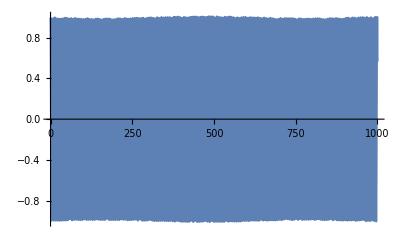

```mathematica
Plot[%,{t,0.,1000.}]
```

```mathematica
ϵ:=.01
```

```mathematica
ω=.01
```

0.01

```mathematica
Clear[ω]
```

```mathematica
Clear[ϵ]
```

```mathematica
Clear[u1]
```

```mathematica
u0:=f[τ]Cos[t]+g[τ]Sin[t]
```

```mathematica
2D[D[u0,t],τ]+D[D[u0,t],t]Sin[ω t]+2ω D[u0,t]Cos[ω t]
```

2 ω Cos[t ω] (Cos[t] g[τ]-f[τ] Sin[t])+(-Cos[t] f[τ]-g[τ] Sin[t]) Sin[t ω]+2 (-Sin[t] f'[τ]+Cos[t] g'[τ])

```mathematica
TrigReduce[2 ω Cos[t ω] (Cos[t] g[τ]-f[τ] Sin[t])+(-Cos[t] f[τ]-g[τ] Sin[t]) Sin[t ω]+2 (-Sin[t] f'[τ]+Cos[t] g'[τ])]
```

1/2 (-Cos[t-t ω] g[τ]+2 ω Cos[t-t ω] g[τ]+Cos[t+t ω] g[τ]+2 ω Cos[t+t ω] g[τ]+f[τ] Sin[t-t ω]-2 ω f[τ] Sin[t-t ω]-f[τ] Sin[t+t ω]-2 ω f[τ] Sin[t+t ω]-4 Sin[t] f'[τ]+4 Cos[t] g'[τ])

```mathematica
Simplify[%174]
```

-f[τ] (2 ω Cos[t ω] Sin[t]+Cos[t] Sin[t ω])+g[τ] (2 ω Cos[t] Cos[t ω]-Sin[t] Sin[t ω])-2 Sin[t] f'[τ]+2 Cos[t] g'[τ]

```mathematica
DSolve[D[D[u1[t,τ],t],t]+u1[t,τ]-f (2 ω Cos[t ω] Sin[t]+Cos[t] Sin[t ω])+g(2 ω Cos[t] Cos[t ω]-Sin[t] Sin[t ω])==0,u1[t,τ],{{t,0,100},{τ,0,10}}]
```

{{u1[t,τ]→1/(2 ω (-4+ω^2))(-4 g Cos[t] Cos[t ω]+g ω^2 Cos[t] Cos[t ω]+3 g ω^2 Cos[t] Cos[2 t] Cos[t ω]+4 f Cos[t ω] Sin[t]-f ω^2 Cos[t ω] Sin[t]+3 f ω^2 Cos[2 t] Cos[t ω] Sin[t]-3 f ω^2 Cos[t] Cos[t ω] Sin[2 t]+3 g ω^2 Cos[t ω] Sin[t] Sin[2 t]+8 f ω Cos[t] Sin[t ω]-2 f ω^3 Cos[t] Sin[t ω]-2 f ω Cos[t] Cos[2 t] Sin[t ω]+2 f ω^3 Cos[t] Cos[2 t] Sin[t ω]+8 g ω Sin[t] Sin[t ω]-2 g ω^3 Sin[t] Sin[t ω]+2 g ω Cos[2 t] Sin[t] Sin[t ω]-2 g ω^3 Cos[2 t] Sin[t] Sin[t ω]-2 g ω Cos[t] Sin[2 t] Sin[t ω]+2 g ω^3 Cos[t] Sin[2 t] Sin[t ω]-2 f ω Sin[t] Sin[2 t] Sin[t ω]+2 f ω^3 Sin[t] Sin[2 t] Sin[t ω])+Cos[t] C[1][τ]+Sin[t] C[2][τ]}}

```mathematica
Simplify[%178]
```

{{u1[t,τ]→1/(ω (-4+ω^2))(-2 g Cos[t] Cos[t ω]+2 g ω^2 Cos[t] Cos[t ω]+2 f Cos[t ω] Sin[t]-2 f ω^2 Cos[t ω] Sin[t]+3 f ω Cos[t] Sin[t ω]+3 g ω Sin[t] Sin[t ω]+ω (-4+ω^2) Cos[t] C[1][τ]+ω (-4+ω^2) Sin[t] C[2][τ])}}

```mathematica
u1:=1/(ω (-4+ω^2))(-2 g Cos[t] Cos[t ω]+2 g ω^2 Cos[t] Cos[t ω]+2 f Cos[t ω] Sin[t]-2 f ω^2 Cos[t ω] Sin[t]+3 f ω Cos[t] Sin[t ω]+3 g ω Sin[t] Sin[t ω]+ω (-4+ω^2) Cos[t] C[1][τ]+ω (-4+ω^2) Sin[t] C[2][τ])
```

```mathematica
TrigReduce[-2 g Cos[t] Cos[t ω]+2 g ω^2 Cos[t] Cos[t ω]+2 f Cos[t ω] Sin[t]-2 f ω^2 Cos[t ω] Sin[t]+3 f ω Cos[t] Sin[t ω]+3 g ω Sin[t] Sin[t ω]]
```

1/2 (-2 g Cos[t-t ω]+3 g ω Cos[t-t ω]+2 g ω^2 Cos[t-t ω]-2 g Cos[t+t ω]-3 g ω Cos[t+t ω]+2 g ω^2 Cos[t+t ω]+2 f Sin[t-t ω]-3 f ω Sin[t-t ω]-2 f ω^2 Sin[t-t ω]+2 f Sin[t+t ω]+3 f ω Sin[t+t ω]-2 f ω^2 Sin[t+t ω])

```mathematica
Simplify[%183]
```

Cos[t] (2 g (-1+ω^2) Cos[t ω]+3 f ω Sin[t ω])+Sin[t] (-2 f (-1+ω^2) Cos[t ω]+3 g ω Sin[t ω])

```mathematica
2D[D[u1,t],τ]+D[D[u1,t],t]Sin[ω t]+2ω D[u1,t]Cos[ω t]
```

1/(-4+ω^2)2 Cos[t ω] (2 f Cos[t] Cos[t ω]+f ω^2 Cos[t] Cos[t ω]+2 g Cos[t ω] Sin[t]+g ω^2 Cos[t ω] Sin[t]+5 g ω Cos[t] Sin[t ω]-2 g ω^3 Cos[t] Sin[t ω]-5 f ω Sin[t] Sin[t ω]+2 f ω^3 Sin[t] Sin[t ω]-ω (-4+ω^2) Sin[t] C[1][τ]+ω (-4+ω^2) Cos[t] C[2][τ])+1/(ω (-4+ω^2))Sin[t ω] (2 g Cos[t] Cos[t ω]+6 g ω^2 Cos[t] Cos[t ω]-2 g ω^4 Cos[t] Cos[t ω]-2 f Cos[t ω] Sin[t]-6 f ω^2 Cos[t ω] Sin[t]+2 f ω^4 Cos[t ω] Sin[t]-7 f ω Cos[t] Sin[t ω]+f ω^3 Cos[t] Sin[t ω]-7 g ω Sin[t] Sin[t ω]+g ω^3 Sin[t] Sin[t ω]-ω (-4+ω^2) Cos[t] C[1][τ]-ω (-4+ω^2) Sin[t] C[2][τ])+(2 (-ω (-4+ω^2) Sin[t] C[1]'[τ]+ω (-4+ω^2) Cos[t] C[2]'[τ]))/(ω (-4+ω^2))

```mathematica
Simplify[TrigReduce[%]]
```

1/(2 ω (-4+ω^2))(-3 f ω Cos[t]+3 f ω^3 Cos[t]+11 f ω Cos[t] Cos[t ω]^2+f ω^3 Cos[t] Cos[t ω]^2-3 g ω Sin[t]+3 g ω^3 Sin[t]+11 g ω Cos[t ω]^2 Sin[t]+g ω^3 Cos[t ω]^2 Sin[t]-11 f ω Cos[t] Sin[t ω]^2-f ω^3 Cos[t] Sin[t ω]^2-11 g ω Sin[t] Sin[t ω]^2-g ω^3 Sin[t] Sin[t ω]^2+2 g Cos[t] Sin[2 t ω]+16 g ω^2 Cos[t] Sin[2 t ω]-6 g ω^4 Cos[t] Sin[2 t ω]-2 f Sin[t] Sin[2 t ω]-16 f ω^2 Sin[t] Sin[2 t ω]+6 f ω^4 Sin[t] Sin[2 t ω]-2 ω (-4+ω^2) (2 ω Cos[t ω] Sin[t]+Cos[t] Sin[t ω]) C[1][τ]+ω (-4+ω^2) (4 ω Cos[t] Cos[t ω]-2 Sin[t] Sin[t ω]) C[2][τ]+16 ω Sin[t] C[1]'[τ]-4 ω^3 Sin[t] C[1]'[τ]-16 ω Cos[t] C[2]'[τ]+4 ω^3 Cos[t] C[2]'[τ])

```mathematica
DSolve[D[D[u1[t,τ],t],t]+u1[t,τ]+1/2 (f Sin[t+ϕ-t ω]-2 f ω Sin[t+ϕ-t ω]-f Sin[t+ϕ+t ω]-2 f ω Sin[t+ϕ+t ω])==0,u1[t,τ],{{t,0,100},{τ,0,10}}]
```

{{u1[t,τ]→1/(4 ω (-4+ω^2))(-2 f ω Cos[ϕ-t (-2+ω)] Sin[t]+3 f ω^2 Cos[ϕ-t (-2+ω)] Sin[t]+2 f ω^3 Cos[ϕ-t (-2+ω)] Sin[t]+8 f Cos[ϕ] Cos[t ω] Sin[t]-2 f ω^2 Cos[ϕ] Cos[t ω] Sin[t]+2 f ω Cos[ϕ+t (2+ω)] Sin[t]+3 f ω^2 Cos[ϕ+t (2+ω)] Sin[t]-2 f ω^3 Cos[ϕ+t (2+ω)] Sin[t]+8 f Cos[t] Cos[t ω] Sin[ϕ]-2 f ω^2 Cos[t] Cos[t ω] Sin[ϕ]+2 f ω Cos[t] Sin[ϕ-t (-2+ω)]-3 f ω^2 Cos[t] Sin[ϕ-t (-2+ω)]-2 f ω^3 Cos[t] Sin[ϕ-t (-2+ω)]+16 f ω Cos[t] Cos[ϕ] Sin[t ω]-4 f ω^3 Cos[t] Cos[ϕ] Sin[t ω]-16 f ω Sin[t] Sin[ϕ] Sin[t ω]+4 f ω^3 Sin[t] Sin[ϕ] Sin[t ω]-2 f ω Cos[t] Sin[ϕ+t (2+ω)]-3 f ω^2 Cos[t] Sin[ϕ+t (2+ω)]+2 f ω^3 Cos[t] Sin[ϕ+t (2+ω)])+Cos[t] C[1][τ]+Sin[t] C[2][τ]}}

```mathematica
Simplify[%162]
```

{{u1[t,τ]→(f ((2-3 ω-2 ω^2) Sin[t+ϕ-t ω]+(2+3 ω-2 ω^2) Sin[t+ϕ+t ω])+2 ω (-4+ω^2) Cos[t] C[1][τ]+2 ω (-4+ω^2) Sin[t] C[2][τ])/(2 ω (-4+ω^2))}}

```mathematica
u1
```

u1

```mathematica
u1:=(f ((2-3 ω-2 ω^2) Sin[t+ϕ-t ω]+(2+3 ω-2 ω^2) Sin[t+ϕ+t ω])+2 ω (-4+ω^2) Cos[t] C[1][τ]+2 ω (-4+ω^2) Sin[t] C[2][τ])/(2 ω (-4+ω^2))
```

```mathematica
2D[D[u1,t],τ]+D[D[u1,t],t]Sin[ω t]+2ω D[u1,t]Cos[ω t]
```

(Cos[t ω] (f ((1-ω) (2-3 ω-2 ω^2) Cos[t+ϕ-t ω]+(1+ω) (2+3 ω-2 ω^2) Cos[t+ϕ+t ω])-2 ω (-4+ω^2) Sin[t] C[1][τ]+2 ω (-4+ω^2) Cos[t] C[2][τ]))/(-4+ω^2)+(Sin[t ω] (f (-(1-ω)^2 (2-3 ω-2 ω^2) Sin[t+ϕ-t ω]-(1+ω)^2 (2+3 ω-2 ω^2) Sin[t+ϕ+t ω])-2 ω (-4+ω^2) Cos[t] C[1][τ]-2 ω (-4+ω^2) Sin[t] C[2][τ]))/(2 ω (-4+ω^2))+(-2 ω (-4+ω^2) Sin[t] C[1]'[τ]+2 ω (-4+ω^2) Cos[t] C[2]'[τ])/(ω (-4+ω^2))

```mathematica
Simplify[TrigReduce[%]]
```

1/(4 ω (-4+ω^2))(-6 f ω Cos[t+ϕ]+6 f ω^3 Cos[t+ϕ]-2 f Cos[t+ϕ-2 t ω]+11 f ω Cos[t+ϕ-2 t ω]-16 f ω^2 Cos[t+ϕ-2 t ω]+f ω^3 Cos[t+ϕ-2 t ω]+6 f ω^4 Cos[t+ϕ-2 t ω]+2 f Cos[t+ϕ+2 t ω]+11 f ω Cos[t+ϕ+2 t ω]+16 f ω^2 Cos[t+ϕ+2 t ω]+f ω^3 Cos[t+ϕ+2 t ω]-6 f ω^4 Cos[t+ϕ+2 t ω]-4 ω (-4+ω^2) (2 ω Cos[t ω] Sin[t]+Cos[t] Sin[t ω]) C[1][τ]+4 ω (-4+ω^2) (2 ω Cos[t] Cos[t ω]-Sin[t] Sin[t ω]) C[2][τ]+32 ω Sin[t] C[1]'[τ]-8 ω^3 Sin[t] C[1]'[τ]-32 ω Cos[t] C[2]'[τ]+8 ω^3 Cos[t] C[2]'[τ])

```mathematica
TrigReduce[2 ω Cos[t] Cos[t ω]-Sin[t] Sin[t ω]]
```

1/2 (-Cos[t-t ω]+2 ω Cos[t-t ω]+Cos[t+t ω]+2 ω Cos[t+t ω])

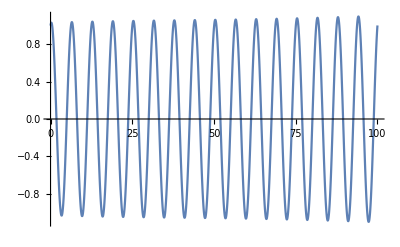

```mathematica
Plot[Cos[t]+ϵ/(ω(ω^2-4))((1-ω^2)2Cos[ω t]Sin[t]+3ω Cos[t]Sin[ω t])+(ϵ^2 t 3(1-ω^2)Cos[t])/(4ω(ω-4)),{t,0,100}]
```

```mathematica
ω=-.02
```

-0.02

```mathematica
Cos[λ x]Cos[λ c T]
```

Cos[c T λ] Cos[x λ]

```mathematica
Cos[x λ] Sin[c T λ]
```

Cos[x λ] Sin[c T λ]

```mathematica
TrigReduce[%]
```

1/2 (Cos[c T λ-x λ]+Cos[c T λ+x λ])

```mathematica
u:=a[τ]Cos[x-c[τ]T]+a1[τ]Sin[x-c[τ]T]+b[τ]Cos[x+c[τ]T]+b1[τ]Sin[x+c[τ]T]
```

```mathematica
D[D[u,T],τ]
```

c[τ] Sin[x-T c[τ]] a'[τ]-c[τ] Cos[x-T c[τ]] a1'[τ]-c[τ] Sin[x+T c[τ]] b'[τ]+c[τ] Cos[x+T c[τ]] b1'[τ]-a1[τ] Cos[x-T c[τ]] c'[τ]-T a[τ] c[τ] Cos[x-T c[τ]] c'[τ]+b1[τ] Cos[x+T c[τ]] c'[τ]-T b[τ] c[τ] Cos[x+T c[τ]] c'[τ]+a[τ] Sin[x-T c[τ]] c'[τ]-T a1[τ] c[τ] Sin[x-T c[τ]] c'[τ]-b[τ] Sin[x+T c[τ]] c'[τ]-T b1[τ] c[τ] Sin[x+T c[τ]] c'[τ]

```mathematica
Simplify[%]
```

(-a1[τ] Cos[x-T c[τ]]+b1[τ] Cos[x+T c[τ]]+a[τ] Sin[x-T c[τ]]-b[τ] Sin[x+T c[τ]]) c'[τ]-c[τ] (-Sin[x-T c[τ]] a'[τ]+Cos[x-T c[τ]] a1'[τ]+Sin[x+T c[τ]] b'[τ]-Cos[x+T c[τ]] b1'[τ]+T a[τ] Cos[x-T c[τ]] c'[τ]+T b[τ] Cos[x+T c[τ]] c'[τ]+T a1[τ] Sin[x-T c[τ]] c'[τ]+T b1[τ] Sin[x+T c[τ]] c'[τ])

```mathematica
DSolve[{c[τ] b1'[τ]+b1[τ]D[c[τ],τ]-T b0[τ]c[τ]D[c[τ],τ]==0, -c[τ]b0'[τ]-b0[τ]D[c[τ],τ]-T b1[τ]c[τ]D[c[τ],τ]==0 },{b0[τ],b1[τ]},{τ,0,100}]
```

DSolve[{c[τ] b1'[τ]+b1[τ] c'[τ]-T b0[τ] c[τ] c'[τ]==0,-c[τ] b0'[τ]-b0[τ] c'[τ]-T b1[τ] c[τ] c'[τ]==0},{b0[τ],b1[τ]},{τ,0,100}]

```mathematica
D[c[τ],τ]
```

c'[τ]

```mathematica
c[τ]
```

c[τ]

```mathematica
ClearAll
```

ClearAll

```mathematica
c'[τ]
```

1

```mathematica
c
```

c

```mathematica
c[τ]
```

τ

```mathematica
c=τ
```

τ

```mathematica
Clear[c'[τ]]
```

Clear::ssym: c'[τ] is not a symbol or a string.

```mathematica
c[τ]:=τ
```

```mathematica
c'[τ]:=1
```

```mathematica
DSolve[{-c[τ]b0'[τ]-b0[τ]D[c[τ],τ]-T b1[τ]c[τ]D[c[τ],τ]==0,c[τ]b1'[τ]+b1[τ]D[c[τ],τ]-T b0[τ]c[τ]D[c[τ],τ]==0},{b0[τ],b1[τ]},{τ,0,100}]
```

DSolve[{-c[τ] b0'[τ]-b0[τ] c'[τ]-T b1[τ] c[τ] c'[τ]==0,c[τ] b1'[τ]+b1[τ] c'[τ]-T b0[τ] c[τ] c'[τ]==0},{b0[τ],b1[τ]},{τ,0,100}]

```mathematica
a0[τ]:=(c1 Cos[c[τ]T]+c2 Sin[c[τ]T])/c[τ]
```

```mathematica
a1[τ]:=(c2 Cos[c[τ]T]-c1 Sin[c[τ]T])/c[τ]
```

```mathematica
b0[τ]:=(d2 Cos[c[τ]T]-d1 Sin[c[τ]T])/c[τ]
```

SetDelayed::write: Tag Times in (d2 Cos[T c[τ]]-d1 Sin[T c[τ]])/c[τ][τ] is Protected.

$Failed

```mathematica
b1[τ]:=(d1 Cos[c[τ]T]+d2 Sin[c[τ]T])/c[τ]
```

```mathematica
Simplify[TrigReduce[a0[τ]Cos[x-c[τ]T]+a1[τ]Cos[x+c[τ]T]+b0 Sin[x-c[τ]T]+b1[τ]Sin[x+c[τ]T]]]
```

1/(2 c[τ])((c1+c2+d1+d2) Cos[x]+(c1-d1) Cos[x-2 T c[τ]]+c2 Cos[x+2 T c[τ]]-d2 Cos[x+2 T c[τ]]+c1 Sin[x]+c2 Sin[x]+d1 Sin[x]+d2 Sin[x]-c2 Sin[x-2 T c[τ]]+d2 Sin[x-2 T c[τ]]-c1 Sin[x+2 T c[τ]]+d1 Sin[x+2 T c[τ]])

```mathematica
u0
```

u0

```mathematica
u
```

u

```mathematica
Clear[a0,a1,b0,b1]
```

```mathematica
u0:=a0[τ]Sin[T-x]+a1[τ]Sin[T+x]+b0[τ]Cos[T-x]+b1[τ]Cos[T+x]
```

```mathematica
D[c[τ],τ]/c[τ] D[u0,T]+2D[D[u0,T],τ]
```

2 (Cos[T-x] a0'[τ]+Cos[T+x] a1'[τ]-Sin[T-x] b0'[τ]-Sin[T+x] b1'[τ])+1/c[τ](a0[τ] Cos[T-x]+a1[τ] Cos[T+x]-b0[τ] Sin[T-x]-b1[τ] Sin[T+x]) c'[τ]

```mathematica
Simplify[TrigReduce[%]]
```

1/c[τ](2 c[τ] (Cos[T-x] a0'[τ]+Cos[T+x] a1'[τ]-Sin[T-x] b0'[τ]-Sin[T+x] b1'[τ])+(a0[τ] Cos[T-x]+a1[τ] Cos[T+x]-b0[τ] Sin[T-x]-b1[τ] Sin[T+x]) c'[τ])

```mathematica
u0:=f0[τ]Cos[T+ϕ[τ]]
```

```mathematica
v0:=f0[τ]Sin[T+ϕ[τ]]
```

```mathematica
D[u0,τ]+u0
```

Cos[T+ϕ[τ]] f0[τ]+Cos[T+ϕ[τ]] f0'[τ]-f0[τ] Sin[T+ϕ[τ]] ϕ'[τ]

```mathematica
D[v0,τ]+v0^3
```

f0[τ]^3 Sin[T+ϕ[τ]]^3+Sin[T+ϕ[τ]] f0'[τ]+Cos[T+ϕ[τ]] f0[τ] ϕ'[τ]

```mathematica
TrigReduce[f0[τ]^3 Sin[T+ϕ[τ]]^3+Sin[T+ϕ[τ]] D[f0[τ],τ]+Cos[T+ϕ[τ]] f0[τ] ϕ[τ]]
```

-(-6 Sin[T]+7 ⅇ^τ Sin[T]+2 Sin[3 T])/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Simplify[-(-6 Sin[T]+7 ⅇ^τ Sin[T]+2 Sin[3 T])/((-3+7 ⅇ^τ)^(3/2))]
```

-((-4+7 ⅇ^τ+4 Cos[2 T]) Sin[T])/((-3+7 ⅇ^τ)^(3/2))

```mathematica
f0[τ]:=2/Sqrt[7Exp[τ]-3]
```

```mathematica
ϕ[τ]:=0
```

```mathematica
v0
```

(2 Sin[T])/(√(-3+7 ⅇ^τ))

```mathematica
v1:=f1[τ]Cos[T+ψ[τ]]-(3Cos[T]Cos[2T])/(2(7Exp[τ]-3)^(3/2))
```

```mathematica
u1=D[v1,T]+D[v0,τ]+v0^3
```

Cos[T] g1[τ]-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Simplify[u1]
```

((14-14 ⅇ^τ+Cos[2 T]) Sin[T]-2 (-3+7 ⅇ^τ)^(3/2) f1[τ] Sin[T+ψ[τ]])/(2 (-3+7 ⅇ^τ)^(3/2))

```mathematica
TrigReduce[((14-14 ⅇ^τ+Cos[2 T]) Sin[T]-2 (-3+7 ⅇ^τ)^(3/2) f1[τ] Sin[T+ψ[τ]])/(2 (-3+7 ⅇ^τ)^(3/2))]
```

-1/(4 (-3+7 ⅇ^τ)^(3/2))(-27 Sin[T]+28 ⅇ^τ Sin[T]-Sin[3 T]-12 √(-3+7 ⅇ^τ) f1[τ] Sin[T+ψ[τ]]+28 ⅇ^τ √(-3+7 ⅇ^τ) f1[τ] Sin[T+ψ[τ]])

```mathematica
Simplify[-1/(4 (-3+7 ⅇ^τ)^(3/2))(-27 Sin[T]+28 ⅇ^τ Sin[T]-Sin[3 T]-12 √(-3+7 ⅇ^τ) f1[τ] Sin[T+ψ[τ]]+28 ⅇ^τ √(-3+7 ⅇ^τ) f1[τ] Sin[T+ψ[τ]])]
```

((14-14 ⅇ^τ+Cos[2 T]) Sin[T]-2 (-3+7 ⅇ^τ)^(3/2) f1[τ] Sin[T+ψ[τ]])/(2 (-3+7 ⅇ^τ)^(3/2))

```mathematica
u1:=((14-14 ⅇ^τ+Cos[2 T]) Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))
```

```mathematica
Clear[ω]
```

```mathematica
3 v1^2 D[v1,T]+2ω D[D[v0,T],T]+D[D[v1,T],τ]+u1+D[u1,τ]
```

-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-(4 ω Sin[T])/(√(-3+7 ⅇ^τ))-(63 ⅇ^τ Cos[2 T] Sin[T])/(4 (-3+7 ⅇ^τ)^(5/2))-(21 ⅇ^τ (14-14 ⅇ^τ+Cos[2 T]) Sin[T])/(4 (-3+7 ⅇ^τ)^(5/2))+((14-14 ⅇ^τ+Cos[2 T]) Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))-(63 ⅇ^τ Cos[T] Sin[2 T])/(2 (-3+7 ⅇ^τ)^(5/2))+(27 Cos[T]^2 Cos[2 T]^2 ((3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))))/(4 (-3+7 ⅇ^τ)^3)

```mathematica
Simplify[TrigReduce[%]]
```

```mathematica
1/(128 (-3+7 ⅇ^τ)^(9/2))(-22815+96768 ⅇ^τ-84672 ⅇ^(2 τ)+43904 ⅇ^(3 τ)-153664 ⅇ^(4 τ)-41472 ω+387072 ⅇ^τ ω-1354752 ⅇ^(2 τ) ω+2107392 ⅇ^(3 τ) ω-1229312 ⅇ^(4 τ) ω+(702-48384 ⅇ^τ+254016 ⅇ^(2 τ)-307328 ⅇ^(3 τ)) Cos[2 T]+1620 Cos[4 T]+810 Cos[6 T]+243 Cos[8 T]) Sin[T]
```

1/(128 (-3+7 ⅇ^τ)^(9/2))(-27999+145152 ⅇ^τ-254016 ⅇ^(2 τ)+307328 ⅇ^(3 τ)-307328 ⅇ^(4 τ)+(702-48384 ⅇ^τ+254016 ⅇ^(2 τ)-307328 ⅇ^(3 τ)) Cos[2 T]+1620 Cos[4 T]+810 Cos[6 T]+243 Cos[8 T]) Sin[T]

```mathematica
Simplify[1/(128 (-3+7 ⅇ^τ)^(9/2))(-27999+145152 ⅇ^τ-254016 ⅇ^(2 τ)+307328 ⅇ^(3 τ)-307328 ⅇ^(4 τ)+(702-48384 ⅇ^τ+254016 ⅇ^(2 τ)-307328 ⅇ^(3 τ)) Cos[2 T]+1620 Cos[4 T]+810 Cos[6 T]+243 Cos[8 T]) Sin[T]]
```

1/(128 (-3+7 ⅇ^τ)^(9/2))(-27999+145152 ⅇ^τ-254016 ⅇ^(2 τ)+307328 ⅇ^(3 τ)-307328 ⅇ^(4 τ)+(702-48384 ⅇ^τ+254016 ⅇ^(2 τ)-307328 ⅇ^(3 τ)) Cos[2 T]+1620 Cos[4 T]+810 Cos[6 T]+243 Cos[8 T]) Sin[T]

```mathematica
ω:=1/8
```

```mathematica
-u1-ω D[u0,T]-D[u1,τ]
```

-(147 ⅇ^(2 τ) Sin[T])/(2 (-3+7 ⅇ^τ)^(5/2))+(14 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(2 ω Sin[T])/(√(-3+7 ⅇ^τ))+(63 ⅇ^τ Cos[2 T] Sin[T])/(4 (-3+7 ⅇ^τ)^(5/2))-(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(84 ⅇ^τ Sin[T]^3)/((-3+7 ⅇ^τ)^(5/2))-(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(63 ⅇ^τ Cos[T] Sin[2 T])/(2 (-3+7 ⅇ^τ)^(5/2))-(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))+f1[τ] Sin[T+ψ[τ]]+Sin[T+ψ[τ]] f1'[τ]+Cos[T+ψ[τ]] f1[τ] ψ'[τ]

```mathematica
Simplify[TrigReduce[%]]
```

1/(8 (-3+7 ⅇ^τ)^3)(2 √(-3+7 ⅇ^τ) (84+72 ω+98 ⅇ^(2 τ) (1+4 ω)-14 ⅇ^τ (5+24 ω)+(6+7 ⅇ^τ) Cos[2 T]) Sin[T]+8 (-3+7 ⅇ^τ)^3 Sin[T+ψ[τ]] f1'[τ]+8 (-3+7 ⅇ^τ)^3 f1[τ] (Sin[T+ψ[τ]]+Cos[T+ψ[τ]] ψ'[τ]))

```mathematica
Limit[1/(8 (-3+7 ⅇ^τ)^3)(2 √(-3+7 ⅇ^τ) (84+72 ω+98 ⅇ^(2 τ) (1+4 ω)-14 ⅇ^τ (5+24 ω)+(6+7 ⅇ^τ) Cos[2 T]) Sin[T]),τ->∞]
```

0

```mathematica
Clear[ω]
```

```mathematica
TrigReduce[(((6+7 ⅇ^τ) Cos[2 T]) Sin[T])]
```

-1/2 (6+7 ⅇ^τ) (Sin[T]-Sin[3 T])

```mathematica
u1
```

-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]]

```mathematica
v1
```

-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T+ψ[τ]] f1[τ]

```mathematica
-v1^3-ω D[v0,T]-D[v1,τ]
```

-(2 ω Cos[T])/(√(-3+7 ⅇ^τ))-(63 ⅇ^τ Cos[T] Cos[2 T])/(4 (-3+7 ⅇ^τ)^(5/2))-(-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T+ψ[τ]] f1[τ])^3-Cos[T+ψ[τ]] f1'[τ]+f1[τ] Sin[T+ψ[τ]] ψ'[τ]

```mathematica
TrigReduce[-(2 ω Cos[T])/(√(-3+7 ⅇ^τ))-(63 ⅇ^τ Cos[T] Cos[2 T])/(4 (-3+7 ⅇ^τ)^(5/2))-(-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T+ψ[τ]] f1[τ])^3-Cos[T+ψ[τ]] f1'[τ]+f1[τ] Sin[T+ψ[τ]] ψ'[τ]]
```

```mathematica
Simplify[TrigReduce[%]]
```

```mathematica
-1/(256 (-3+7 ⅇ^τ)^5)(2 √(-3+7 ⅇ^τ) Cos[T] (-81+20736 ω-193536 ⅇ^τ ω+677376 ⅇ^(2 τ) ω-1053696 ⅇ^(3 τ) ω+614656 ⅇ^(4 τ) ω+18 (-9+1008 ⅇ^τ-4704 ⅇ^(2 τ)+5488 ⅇ^(3 τ)) Cos[2 T]-108 Cos[4 T]-54 Cos[6 T]-27 Cos[8 T])-576 (-3+7 ⅇ^τ)^(7/2) (Cos[T]+Cos[3 T]) Cos[T+ψ[τ]]^2 f1[τ]^2+256 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]]^3 f1[τ]^3+256 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]] f1'[τ]+4 (3-7 ⅇ^τ)^2 f1[τ] (108 (Cos[T]+Cos[3 T])^2 Cos[T+ψ[τ]]-64 (-3+7 ⅇ^τ)^3 Sin[T+ψ[τ]] ψ'[τ]))
```

-1/(256 (-3+7 ⅇ^τ)^5)(2 √(-3+7 ⅇ^τ) Cos[T] (2511-24192 ⅇ^τ+84672 ⅇ^(2 τ)-131712 ⅇ^(3 τ)+76832 ⅇ^(4 τ)+18 (-9+1008 ⅇ^τ-4704 ⅇ^(2 τ)+5488 ⅇ^(3 τ)) Cos[2 T]-108 Cos[4 T]-54 Cos[6 T]-27 Cos[8 T])-576 (-3+7 ⅇ^τ)^(7/2) (Cos[T]+Cos[3 T]) Cos[T+ψ[τ]]^2 f1[τ]^2+256 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]]^3 f1[τ]^3+256 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]] f1'[τ]+4 (3-7 ⅇ^τ)^2 f1[τ] (108 (Cos[T]+Cos[3 T])^2 Cos[T+ψ[τ]]-64 (-3+7 ⅇ^τ)^3 Sin[T+ψ[τ]] ψ'[τ]))

```mathematica
Simplify[%70]
```

-1/(256 (-3+7 ⅇ^τ)^5)(2 √(-3+7 ⅇ^τ) Cos[T] (2511-24192 ⅇ^τ+84672 ⅇ^(2 τ)-131712 ⅇ^(3 τ)+76832 ⅇ^(4 τ)+18 (-9+1008 ⅇ^τ-4704 ⅇ^(2 τ)+5488 ⅇ^(3 τ)) Cos[2 T]-108 Cos[4 T]-54 Cos[6 T]-27 Cos[8 T])-576 (-3+7 ⅇ^τ)^(7/2) (Cos[T]+Cos[3 T]) Cos[T+ψ[τ]]^2 f1[τ]^2+256 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]]^3 f1[τ]^3+256 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]] f1'[τ]+4 (3-7 ⅇ^τ)^2 f1[τ] (108 (Cos[T]+Cos[3 T])^2 Cos[T+ψ[τ]]-64 (-3+7 ⅇ^τ)^3 Sin[T+ψ[τ]] ψ'[τ]))

```mathematica
Clear[ω]
```

```mathematica
u1
```

-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]]

```mathematica
v1
```

-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T+ψ[τ]] f1[τ]

```mathematica
-(3 v1^2 D[v1,T]+2ω D[D[v0,T],T]+D[D[v1,T],τ]+D[u1,τ]+u1)
```

-(147 ⅇ^(2 τ) Sin[T])/(2 (-3+7 ⅇ^τ)^(5/2))+(14 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(4 ω Sin[T])/(√(-3+7 ⅇ^τ))+(63 ⅇ^τ Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(5/2))-(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(84 ⅇ^τ Sin[T]^3)/((-3+7 ⅇ^τ)^(5/2))-(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(63 ⅇ^τ Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(5/2))-(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))+f1[τ] Sin[T+ψ[τ]]-3 (-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T+ψ[τ]] f1[τ])^2 ((3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]])+2 Sin[T+ψ[τ]] f1'[τ]+2 Cos[T+ψ[τ]] f1[τ] ψ'[τ]

```mathematica
Simplify[TrigReduce[%75]]
```

1/(256 (-3+7 ⅇ^τ)^5)(2 √(-3+7 ⅇ^τ) (22815-96768 ⅇ^τ+84672 ⅇ^(2 τ)-43904 ⅇ^(3 τ)+153664 ⅇ^(4 τ)+41472 ω-387072 ⅇ^τ ω+1354752 ⅇ^(2 τ) ω-2107392 ⅇ^(3 τ) ω+1229312 ⅇ^(4 τ) ω+(-702+48384 ⅇ^τ-254016 ⅇ^(2 τ)+307328 ⅇ^(3 τ)) Cos[2 T]-1620 Cos[4 T]-810 Cos[6 T]-243 Cos[8 T]) Sin[T]+768 (-3+7 ⅇ^τ)^5 Cos[T+ψ[τ]]^2 f1[τ]^3 Sin[T+ψ[τ]]-144 (-3+7 ⅇ^τ)^(7/2) f1[τ]^2 (2 Sin[T]+6 Sin[3 T]+Sin[T-2 ψ[τ]]+Sin[T+2 ψ[τ]]+3 Sin[3 T+2 ψ[τ]]+5 Sin[5 T+2 ψ[τ]])+512 (-3+7 ⅇ^τ)^5 Sin[T+ψ[τ]] f1'[τ]+4 (3-7 ⅇ^τ)^2 f1[τ] (81 Sin[T-ψ[τ]]+162 Sin[3 T-ψ[τ]]+135 Sin[5 T-ψ[τ]]-1620 Sin[T+ψ[τ]]+12096 ⅇ^τ Sin[T+ψ[τ]]-28224 ⅇ^(2 τ) Sin[T+ψ[τ]]+21952 ⅇ^(3 τ) Sin[T+ψ[τ]]+243 Sin[3 T+ψ[τ]]+270 Sin[5 T+ψ[τ]]+189 Sin[7 T+ψ[τ]]+128 (-3+7 ⅇ^τ)^3 Cos[T+ψ[τ]] ψ'[τ]))

```mathematica
v0
```

(2 Sin[T])/(√(-3+7 ⅇ^τ))

```mathematica
v1:=-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+f1[τ]Cos[T]+g1[τ]Sin[T]
```

```mathematica
-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+f1[τ]Cos[T]+g1[τ]Sin[T]
```

-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]

```mathematica
u0
```

(2 Cos[T])/(√(-3+7 ⅇ^τ))

```mathematica
u1
```

-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T+ψ[τ]]

```mathematica
ω D[D[v0,T],T]+D[D[v1,T],τ]+6v0 D[v0,T]v1+3 v0^2 D[v1,T]+ω D[u0,T]+D[u1,τ]+u1
```

Cos[T] g1[τ]+(147 ⅇ^(2 τ) Sin[T])/(2 (-3+7 ⅇ^τ)^(5/2))-(14 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-(4 ω Sin[T])/(√(-3+7 ⅇ^τ))-(63 ⅇ^τ Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(5/2))+(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]-(84 ⅇ^τ Sin[T]^3)/((-3+7 ⅇ^τ)^(5/2))+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(24 Cos[T] Sin[T] (-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]))/(-3+7 ⅇ^τ)-(63 ⅇ^τ Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(5/2))+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2))+1/(-3+7 ⅇ^τ)12 Sin[T]^2 (Cos[T] g1[τ]+(3 Cos[2 T] Sin[T])/(2 (-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(3 Cos[T] Sin[2 T])/((-3+7 ⅇ^τ)^(3/2)))-2 Sin[T] f1'[τ]+2 Cos[T] g1'[τ]

```mathematica
Simplify[TrigReduce[%90]]
```

-1/(4 (-3+7 ⅇ^τ)^3)(-4 (3-7 ⅇ^τ)^2 Cos[T] (15+7 ⅇ^τ-18 Cos[2 T]) g1[τ]+81 √(-3+7 ⅇ^τ) Sin[T]-42 ⅇ^τ √(-3+7 ⅇ^τ) Sin[T]+98 ⅇ^(2 τ) √(-3+7 ⅇ^τ) Sin[T]+144 √(-3+7 ⅇ^τ) ω Sin[T]-672 ⅇ^τ √(-3+7 ⅇ^τ) ω Sin[T]+784 ⅇ^(2 τ) √(-3+7 ⅇ^τ) ω Sin[T]+4 (3-7 ⅇ^τ)^2 f1[τ] (7 ⅇ^τ Sin[T]-9 Sin[3 T])-24 √(-3+7 ⅇ^τ) Sin[3 T]+98 ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T]+45 √(-3+7 ⅇ^τ) Sin[5 T]-216 Sin[T] f1'[τ]+1512 ⅇ^τ Sin[T] f1'[τ]-3528 ⅇ^(2 τ) Sin[T] f1'[τ]+2744 ⅇ^(3 τ) Sin[T] f1'[τ]+216 Cos[T] g1'[τ]-1512 ⅇ^τ Cos[T] g1'[τ]+3528 ⅇ^(2 τ) Cos[T] g1'[τ]-2744 ⅇ^(3 τ) Cos[T] g1'[τ])

```mathematica
TrigReduce[-4 (3-7 ⅇ^τ)^2 Cos[T] (15+7 ⅇ^τ-18 Cos[2 T]) g1[τ]]
```

-4 (-3+7 ⅇ^τ)^2 (6 Cos[T]+7 ⅇ^τ Cos[T]-9 Cos[3 T]) g1[τ]

```mathematica
v1[0,0]
```

(-(3 Cos[T] Cos[2 T])/(2 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T])[0,0]

```mathematica
DSolve[-4(3-7Exp[τ])^2(6+7Exp[τ])g1[τ]+(216-1512Exp[τ]+3528Exp[2τ]-2744Exp[3τ])g1'[τ]==0,g1[τ],{τ,0,100}]
```

{{g1[τ]→(ⅇ^τ C[1])/((3-7 ⅇ^τ)^(3/2))}}

```mathematica
DSolve[28(3-7Exp[τ])^2 f1[τ]+f1'[τ](-216+1512Exp[τ]-3528 Exp[2τ]+2744Exp[3τ])==0,f1[τ],{τ,0,100}]
```

{{f1[τ]→((-1)^(5/6) ⅇ^(7 τ/6) C[1])/((-3+7 ⅇ^τ)^(7/6))}}

```mathematica
Simplify[{{f1[τ]->1/(56 (-3+7 ⅇ^τ)^(3/2))(-18 (9+16 ω)+21 ⅇ^τ (81+32 ω)+56 (-1)^(5/6) ⅇ^(7 τ/6) (-3+7 ⅇ^τ)^(1/3) C[1]+7 3^(2/3) ⅇ^τ (3-7 ⅇ^τ)^(1/3) (-215+128 ω) Hypergeometric2F1[-1/6,1/3,5/6,(7 ⅇ^τ)/3])}}]
```

{{f1[τ]→1/(56 (-3+7 ⅇ^τ)^(3/2))(-18 (9+16 ω)+21 ⅇ^τ (81+32 ω)+56 (-1)^(5/6) ⅇ^(7 τ/6) (-3+7 ⅇ^τ)^(1/3) C[1]+7 3^(2/3) ⅇ^τ (3-7 ⅇ^τ)^(1/3) (-215+128 ω) Hypergeometric2F1[-1/6,1/3,5/6,(7 ⅇ^τ)/3])}}

```mathematica
Expand[-ϵ(va+ϵ vb)^3]
```

-va^3 ϵ-3 va^2 vb ϵ^2-3 va vb^2 ϵ^3-vb^3 ϵ^4

```mathematica
u0
```

(2 Cos[T])/(√(-3+7 ⅇ^τ))

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[u0,f0,v0]
```

```mathematica
u0:=f0[τ]Cos[T+ϕ[τ]]
```

```mathematica
v0:=f0[τ]Sin[T+ϕ[τ]]
```

```mathematica
2D[u0,τ]+u0+3 v0^2 u0
```

-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(2 Cos[T])/(√(-3+7 ⅇ^τ))+(24 Cos[T] Sin[T]^2)/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Cos[T]+3 Cos[T] f0^3 Sin[T]^2+2 (Cos[T] D[f0,τ])
```

```mathematica
Cos[T]-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(24 1/4 (Cos[T]-Cos[3 T]))/((-3+7 ⅇ^τ)^(3/2))
```

Cos[T]-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(6 (Cos[T]-Cos[3 T]))/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Cos[T]-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(6 (Cos[T]-Cos[3 T]))/((-3+7 ⅇ^τ)^(3/2))
```

Cos[T]-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(6 (Cos[T]-Cos[3 T]))/((-3+7 ⅇ^τ)^(3/2))

```mathematica
FullSimplify[Cos[T]-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(6 (Cos[T]-Cos[3 T]))/((-3+7 ⅇ^τ)^(3/2))]
```

(Cos[T] (12-14 ⅇ^τ+(-3+7 ⅇ^τ)^(3/2)-12 Cos[2 T]))/((-3+7 ⅇ^τ)^(3/2))

```mathematica
TrigReduce[Cos[T] Sin[T]^2]
```

1/4 (Cos[T]-Cos[3 T])

```mathematica
u0:=Cos[T] 2/(√(-3+7 ⅇ^τ))
```

```mathematica
v0:=2/(√(-3+7 ⅇ^τ)) Sin[T]
```

```mathematica
Simplify[%114]
```

1/((3-7 ⅇ^τ)^2)Cos[T] (9+49 ⅇ^(2 τ)+12 √(-3+7 ⅇ^τ)-14 ⅇ^τ (3+√(-3+7 ⅇ^τ))-12 √(-3+7 ⅇ^τ) Cos[2 T])

```mathematica
DSolve[{4f0[τ]+3(f0[τ])^3+8f0'[τ]==0,f0[0]==1},f0[τ],{τ,0,100}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f0[τ]→2/(√(-3+7 ⅇ^τ))}}

```mathematica
f0:=2/(√(-3+7 ⅇ^τ))
```

SetDelayed::write: Tag Times in 2/(√(-3+7 ⅇ^τ))[τ] is Protected.

```mathematica
2D[u0,τ]+u0+3 v0^2 u0
```

-(14 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(2 Cos[T])/(√(-3+7 ⅇ^τ))+(24 Cos[T] Sin[T]^2)/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Clear[v1]
```

```mathematica
DSolve[D[D[v1[T,τ],T],T]+v1[T,τ]==(6Cos[3T])/(7Exp[τ]-3)^(3/2),v1[T,τ],{{T,0,100},{τ,0,10}}]
```

{{v1[T,τ]→-(3 (4 Cos[T]^3-Cos[T] Cos[4 T]-2 Sin[T] Sin[2 T]-Sin[T] Sin[4 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
TrigReduce[4 Cos[T]^3-Cos[T] Cos[4 T]-2 Sin[T] Sin[2 T]-Sin[T] Sin[4 T]]
```

2 Cos[T]+Cos[3 T]

```mathematica
v1:=3(2 Cos[T]+Cos[3 T])/(4(7Exp[τ]-3)^(3/2))+f1[τ]Cos[T]+g1[τ]Sin[T]
```

```mathematica
Clear[u1,g1,f1]
```

```mathematica
D[v1,T]+D[v0,τ]+v0^3
```

Cos[T] g1[τ]-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
Simplify[Cos[T] g1[τ]-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(8 Sin[T]^3)/((-3+7 ⅇ^τ)^(3/2))+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))]
```

```mathematica
u1:=1/(4 (-3+7 ⅇ^τ)^(3/2))(4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1[τ]-(-1+28 ⅇ^τ+34 Cos[2 T]+4 (-3+7 ⅇ^τ)^(3/2) f1[τ]) Sin[T])
```

```mathematica
Cos[T] g1[τ]-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(8 1/4 (3 Sin[T]-Sin[3 T]))/((-3+7 ⅇ^τ)^(3/2))+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))
```

Cos[T] g1[τ]-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+(2 (3 Sin[T]-Sin[3 T]))/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Simplify[Cos[T] g1[τ]-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))-f1[τ] Sin[T]+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+(2 (3 Sin[T]-Sin[3 T]))/((-3+7 ⅇ^τ)^(3/2))]
```

1/(4 (-3+7 ⅇ^τ)^(3/2))(4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1[τ]-(-1+28 ⅇ^τ+34 Cos[2 T]+4 (-3+7 ⅇ^τ)^(3/2) f1[τ]) Sin[T])

```mathematica
TrigReduce[Sin[T]^3]
```

1/4 (3 Sin[T]-Sin[3 T])

```mathematica
-ω D[u0,T]
```

0

```mathematica
TrigReduce[-(12 Sin[T]^2 ((3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))))/(-3+7 ⅇ^τ)]
```

(9 (3 Sin[T]+4 Sin[3 T]-3 Sin[5 T]))/(4 (-3+7 ⅇ^τ)^(5/2))

```mathematica
u1:=g1[τ]Cos[T]-f1[τ]Sin[T]+((9/2-7Exp[τ])Sin[T]-1/4 Sin[3T])/(7Exp[τ]-3)^(3/2)
```

```mathematica
-D[D[v1,T],τ]-ω D[D[v0,T],T]-6v0 D[v0,T]v1-3 v0^2 D[v1,T]-D[u1,τ]-ω D[u0,T]-u1
```

(4 ω Sin[T])/(√(-3+7 ⅇ^τ))+1/(8 (-3+7 ⅇ^τ)^(5/2))21 ⅇ^τ (4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1[τ]-(-1+28 ⅇ^τ+34 Cos[2 T]+4 (-3+7 ⅇ^τ)^(3/2) f1[τ]) Sin[T])-1/(4 (-3+7 ⅇ^τ)^(3/2))(4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1[τ]-(-1+28 ⅇ^τ+34 Cos[2 T]+4 (-3+7 ⅇ^τ)^(3/2) f1[τ]) Sin[T])-(24 Cos[T] Sin[T] ((3 (2 Cos[T]+Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]))/(-3+7 ⅇ^τ)-(12 Sin[T]^2 (Cos[T] g1[τ]-f1[τ] Sin[T]+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))))/(-3+7 ⅇ^τ)+(63 ⅇ^τ (-2 Sin[T]-3 Sin[3 T]))/(8 (-3+7 ⅇ^τ)^(5/2))+Sin[T] f1'[τ]-Cos[T] g1'[τ]-1/(4 (-3+7 ⅇ^τ)^(3/2))(42 ⅇ^τ √(-3+7 ⅇ^τ) Cos[T] g1[τ]-Sin[T] (28 ⅇ^τ+42 ⅇ^τ √(-3+7 ⅇ^τ) f1[τ]+4 (-3+7 ⅇ^τ)^(3/2) f1'[τ])+4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1'[τ])

```mathematica
Simplify[TrigReduce[%193]]
```

1/(4 (-3+7 ⅇ^τ)^3)(-4 (3-7 ⅇ^τ)^2 Cos[T] (15+7 ⅇ^τ-18 Cos[2 T]) g1[τ]+63 √(-3+7 ⅇ^τ) Sin[T]-168 ⅇ^τ √(-3+7 ⅇ^τ) Sin[T]+98 ⅇ^(2 τ) √(-3+7 ⅇ^τ) Sin[T]+144 √(-3+7 ⅇ^τ) ω Sin[T]-672 ⅇ^τ √(-3+7 ⅇ^τ) ω Sin[T]+784 ⅇ^(2 τ) √(-3+7 ⅇ^τ) ω Sin[T]+4 (3-7 ⅇ^τ)^2 f1[τ] (7 ⅇ^τ Sin[T]-9 Sin[3 T])-51 √(-3+7 ⅇ^τ) Sin[3 T]-154 ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T]-45 √(-3+7 ⅇ^τ) Sin[5 T]-216 Sin[T] f1'[τ]+1512 ⅇ^τ Sin[T] f1'[τ]-3528 ⅇ^(2 τ) Sin[T] f1'[τ]+2744 ⅇ^(3 τ) Sin[T] f1'[τ]+216 Cos[T] g1'[τ]-1512 ⅇ^τ Cos[T] g1'[τ]+3528 ⅇ^(2 τ) Cos[T] g1'[τ]-2744 ⅇ^(3 τ) Cos[T] g1'[τ])

```mathematica
TrigReduce[-(12 Sin[T]^2 ((3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))))/(-3+7 ⅇ^τ)]
```

(9 (3 Sin[T]+4 Sin[3 T]-3 Sin[5 T]))/(4 (-3+7 ⅇ^τ)^(5/2))

```mathematica
TrigReduce[Cos[T] (15+7 ⅇ^τ-18 Cos[2 T])]
```

6 Cos[T]+7 ⅇ^τ Cos[T]-9 Cos[3 T]

```mathematica
DSolve[g1[τ]-(9g1[τ])/(7Exp[τ]-3)-2g1'[τ]==0,g1[τ],{τ,0,10}]
```

{{g1[τ]→(ⅇ^(2 τ) C[1])/((3-7 ⅇ^τ)^(3/2))}}

```mathematica
DSolve[(7Exp[τ])/(7Exp[τ]-3)^(3/2)+(4ω)/(7Exp[τ]-3)^(1/2)+f1[τ]-9/(2(7Exp[τ]-3)^(5/2))-(6f1[τ])/(7Exp[τ]-3)+(9f1[τ])/(7Exp[τ]-3)+27/(4(7Exp[τ]-3)^(5/2))-(63Exp[τ])/(4(7Exp[τ]-3)^(5/2))+(21Exp[τ](9/2-7Exp[τ]))/(2(7Exp[τ]-3)^(5/2))-(9/2-7Exp[τ])/(7Exp[τ]-3)^(3/2)+2f1'[τ]==0,f1[τ],{τ,0,10}]
```

{{f1[τ]→(-8 ⅈ C[1]+√2 (3/(-3+7 ⅇ^τ)+5 ⅈ π-7 τ-16 τ ω+5 Log[-3+7 ⅇ^τ]))/(8 √(-6+14 ⅇ^τ))}}

```mathematica
f1:=(-8 ⅈ C[1]+√2 (3/(-3+7 ⅇ^τ)+5 ⅈ π-7 τ-16 τ ω+5 Log[-3+7 ⅇ^τ]))/(8 √(-6+14 ⅇ^τ))
```

```mathematica
g1:=(ⅇ^(2 τ) C[1])/((3-7 ⅇ^τ)^(3/2))
```

```mathematica
u1=((9/2-7 ⅇ^τ) Sin[T]-1/4 Sin[3 T])/((-3+7 ⅇ^τ)^(3/2))+Cos[T] (ⅇ^(2 τ) C[1])/((3-7 ⅇ^τ)^(3/2))-Sin[T] (-8 ⅈ C[1]+√2 (3/(-3+7 ⅇ^τ)+5 ⅈ π-7 τ-16 τ ω+5 Log[-3+7 ⅇ^τ]))/(8 √(-6+14 ⅇ^τ))
```

(ⅇ^(2 τ) C[1] Cos[T])/((3-7 ⅇ^τ)^(3/2))-((-8 ⅈ C[1]+√2 (3/(-3+7 ⅇ^τ)+5 ⅈ π-7 τ-16 τ ω+5 Log[-3+7 ⅇ^τ])) Sin[T])/(8 √(-6+14 ⅇ^τ))+((9/2-7 ⅇ^τ) Sin[T]-1/4 Sin[3 T])/((-3+7 ⅇ^τ)^(3/2))

```mathematica
Simplify[TrigReduce[u1]]
```

1/(8 (3-7 ⅇ^τ)^2)(8 ⅇ^(2 τ) √(3-7 ⅇ^τ) C[1] Cos[T]+√(-3+7 ⅇ^τ) (31-56 ⅇ^τ+15 ⅈ π-35 ⅈ ⅇ^τ π-27 τ+63 ⅇ^τ τ-12 ⅈ √2 C[1]+28 ⅈ √2 ⅇ^τ C[1]-4 Cos[2 T]-5 (-3+7 ⅇ^τ) Log[-3+7 ⅇ^τ]) Sin[T])

```mathematica
ω=1/8
```

1/8

```mathematica
Clear[ω]
```

```mathematica
DSolve[2g1'[τ]+g1[τ](9/(7Exp[τ]-3)+1)==0,g1[τ],{τ,0,10}]
```

{{g1[τ]→(ⅇ^τ C[1])/((3-7 ⅇ^τ)^(3/2))}}

```mathematica
DSolve[-f1[τ]+(3f1[τ])/(7Exp[τ]-3)+2f1'[τ]==0,f1[τ],{τ,0,10}]
```

{{f1[τ]→-(ⅈ ⅇ^τ C[1])/(√(-3+7 ⅇ^τ))}}

```mathematica
Simplify[{{f1[τ]->(-8 ⅈ C[1]+√2 (3/(-3+7 ⅇ^τ)+5 ⅈ π-9 τ+5 Log[-3+7 ⅇ^τ]))/(8 √(-6+14 ⅇ^τ))}}]
```

{{f1[τ]→(-8 ⅈ C[1]+√2 (3/(-3+7 ⅇ^τ)+5 ⅈ π-9 τ+5 Log[-3+7 ⅇ^τ]))/(8 √(-6+14 ⅇ^τ))}}

```mathematica
-ω D[u0,T]
```

(2 ω Sin[T])/(√(-3+7 ⅇ^τ))

```mathematica
-u1
```

-1/(4 (-3+7 ⅇ^τ)^(3/2))(4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1[τ]-(-1+28 ⅇ^τ+34 Cos[2 T]+4 (-3+7 ⅇ^τ)^(3/2) f1[τ]) Sin[T])

```mathematica
(-63 Exp[τ])/4+4ω(7Exp[τ]-3)^2-9/2+27/4+(21Exp[τ](9-14Exp[τ]))/4+7Exp[τ](7Exp[τ]-3)+(14Exp[τ]-9)/2
```

9/4-(63 ⅇ^τ)/4+21/4 ⅇ^τ (9-14 ⅇ^τ)+7 ⅇ^τ (-3+7 ⅇ^τ)+1/2 (-9+14 ⅇ^τ)+4 (-3+7 ⅇ^τ)^2 ω

```mathematica
Simplify[9/4-(63 ⅇ^τ)/4+21/4 ⅇ^τ (9-14 ⅇ^τ)+7 ⅇ^τ (-3+7 ⅇ^τ)+1/2 (-9+14 ⅇ^τ)+4 (-3+7 ⅇ^τ)^2 ω]
```

1/4 (-9+ⅇ^τ (70-672 ω)+144 ω+98 ⅇ^(2 τ) (-1+8 ω))

```mathematica
DSolve[2g1'[t]+g1'[t](3/(7Exp[t]-3)-1)+1/4 (-9+144 ω)==0,g1[t],{t,0,10}]
```

{{g1[t]→-9/28 (3 ⅇ^-t+7 t) (-1+16 ω)+C[1]}}

```mathematica
Clear[u1,v1]
```

```mathematica
DSolve[D[u1[T,τ],T,T]+u1[T,τ]==-2/(7Exp[τ]-3)^(3/2)Sin[3T],u1[T,τ],{{T,0,100},{τ,0,10}}]
```

{{u1[T,τ]→1/(4 (-3+7 ⅇ^τ)^(3/2))(4 Cos[T]^2 Sin[T]+Cos[4 T] Sin[T]+2 Cos[T] Sin[2 T]-Cos[T] Sin[4 T])+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
TrigReduce[4 Cos[T]^2 Sin[T]+Cos[4 T] Sin[T]+2 Cos[T] Sin[2 T]-Cos[T] Sin[4 T]]
```

2 Sin[T]+Sin[3 T]

```mathematica
u1:=f1[τ]Cos[T]+g1[τ]Sin[T]+(2Sin[T]+Sin[3T])/(4(7Exp[τ]-3)^(3/2))
```

```mathematica
v1=((11/2-7Exp[τ])Cos[T]+3/4 Cos[3T])/(7Exp[τ]-3)^(3/2)-g1[τ]Cos[T]+f1[τ]Sin[T]
```

((11/2-7 ⅇ^τ) Cos[T]+3/4 Cos[3 T])/((-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]

```mathematica
Simplify[v1]
```

(Cos[T] (19-28 ⅇ^τ+6 Cos[2 T]))/(4 (-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]

```mathematica
Simplify[v1]
```

-1/(4 (-3+7 ⅇ^τ)^(3/2))(Cos[T] (-25+28 ⅇ^τ+6 Cos[2 T])+4 (-3+7 ⅇ^τ)^(3/2) Cos[T] g1[τ]-4 (-3+7 ⅇ^τ)^(3/2) f1[τ] Sin[T])

```mathematica
ϵ(a0+ϵ a1+ϵ^2 a2)^3
```

ϵ (a0+a1 ϵ+a2 ϵ^2)^3

```mathematica
Expand[ϵ (a0+a1 ϵ+a2 ϵ^2)^3]
```

a0^3 ϵ+3 a0^2 a1 ϵ^2+3 a0 a1^2 ϵ^3+3 a0^2 a2 ϵ^3+a1^3 ϵ^4+6 a0 a1 a2 ϵ^4+3 a1^2 a2 ϵ^5+3 a0 a2^2 ϵ^5+3 a1 a2^2 ϵ^6+a2^3 ϵ^7

```mathematica
u1
```

Cos[T] f1[τ]+g1[τ] Sin[T]+(2 Sin[T]+Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
v1
```

((11/2-7 ⅇ^τ) Cos[T]+3/4 Cos[3 T])/((-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]

```mathematica
-D[u1,T,τ]-ω D[u0,T,T]-D[u1,T]+D[v1,τ]+ω D[v0,T]+3 v0^2 v1
```

-(7 ⅇ^τ Cos[T])/((-3+7 ⅇ^τ)^(3/2))+(4 ω Cos[T])/(√(-3+7 ⅇ^τ))-(21 ⅇ^τ ((11/2-7 ⅇ^τ) Cos[T]+3/4 Cos[3 T]))/(2 (-3+7 ⅇ^τ)^(5/2))+(21 ⅇ^τ (2 Cos[T]+3 Cos[3 T]))/(8 (-3+7 ⅇ^τ)^(5/2))-(2 Cos[T]+3 Cos[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]+(12 Sin[T]^2 (((11/2-7 ⅇ^τ) Cos[T]+3/4 Cos[3 T])/((-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]))/(-3+7 ⅇ^τ)+2 Sin[T] f1'[τ]-2 Cos[T] g1'[τ]

```mathematica
Simplify[TrigReduce[%33]]
```

1/(4 (-3+7 ⅇ^τ)^3)(63 √(-3+7 ⅇ^τ) Cos[T]-224 ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]+98 ⅇ^(2 τ) √(-3+7 ⅇ^τ) Cos[T]+144 √(-3+7 ⅇ^τ) ω Cos[T]-672 ⅇ^τ √(-3+7 ⅇ^τ) ω Cos[T]+784 ⅇ^(2 τ) √(-3+7 ⅇ^τ) ω Cos[T]-39 √(-3+7 ⅇ^τ) Cos[3 T]+63 ⅇ^τ √(-3+7 ⅇ^τ) Cos[3 T]-9 √(-3+7 ⅇ^τ) Cos[5 T]-4 (3-7 ⅇ^τ)^2 (7 ⅇ^τ Cos[T]-3 Cos[3 T]) g1[τ]+4 (3-7 ⅇ^τ)^2 (3+7 ⅇ^τ-6 Cos[2 T]) f1[τ] Sin[T]-216 Sin[T] f1'[τ]+1512 ⅇ^τ Sin[T] f1'[τ]-3528 ⅇ^(2 τ) Sin[T] f1'[τ]+2744 ⅇ^(3 τ) Sin[T] f1'[τ]+216 Cos[T] g1'[τ]-1512 ⅇ^τ Cos[T] g1'[τ]+3528 ⅇ^(2 τ) Cos[T] g1'[τ]-2744 ⅇ^(3 τ) Cos[T] g1'[τ])

```mathematica
TrigReduce[4 (3-7 ⅇ^τ)^2 (3+7 ⅇ^τ-6 Cos[2 T]) f1[τ] Sin[T]]
```

4 (-3+7 ⅇ^τ)^2 f1[τ] (6 Sin[T]+7 ⅇ^τ Sin[T]-3 Sin[3 T])

```mathematica
D[(11/2-7Exp[τ])/(7Exp[τ]-3)^(3/2),τ]
```

-(21 ⅇ^τ (11/2-7 ⅇ^τ))/(2 (-3+7 ⅇ^τ)^(5/2))-(7 ⅇ^τ)/((-3+7 ⅇ^τ)^(3/2))

```mathematica
3 v0^2 v1
```

(12 Sin[T]^2 (((11/2-7 ⅇ^τ) Cos[T]+3/4 Cos[3 T])/((-3+7 ⅇ^τ)^(3/2))-Cos[T] g1[τ]+f1[τ] Sin[T]))/(-3+7 ⅇ^τ)

```mathematica
TrigReduce[%]
```

1/(-3+7 ⅇ^τ)(-3 Cos[T] g1[τ]+3 Cos[3 T] g1[τ]+9 f1[τ] Sin[T]+(57/8 √(-3+7 ⅇ^τ) Cos[T]-57/8 ⅈ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^2)+(57/8 √(-3+7 ⅇ^τ) Cos[T]+57/8 ⅈ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^2)+(-21/2 ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]-21/2 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^2)+(-21/2 ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]+21/2 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[T])/((-3+7 ⅇ^τ)^2)-3 f1[τ] Sin[3 T]+(-6 √(-3+7 ⅇ^τ) Cos[3 T]-6 ⅈ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^2)+(-6 √(-3+7 ⅇ^τ) Cos[3 T]+6 ⅈ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^2)+(21/2 ⅇ^τ √(-3+7 ⅇ^τ) Cos[3 T]-21/2 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^2)+(21/2 ⅇ^τ √(-3+7 ⅇ^τ) Cos[3 T]+21/2 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T])/((-3+7 ⅇ^τ)^2)+(-9/8 √(-3+7 ⅇ^τ) Cos[5 T]-9/8 ⅈ √(-3+7 ⅇ^τ) Sin[5 T])/((-3+7 ⅇ^τ)^2)+(-9/8 √(-3+7 ⅇ^τ) Cos[5 T]+9/8 ⅈ √(-3+7 ⅇ^τ) Sin[5 T])/((-3+7 ⅇ^τ)^2))

```mathematica
Simplify[%]
```

1/((-3+7 ⅇ^τ)^3)3 Sin[T]^2 (-√(-3+7 ⅇ^τ) Cos[T] (-19+28 ⅇ^τ-6 Cos[2 T])-4 (3-7 ⅇ^τ)^2 Cos[T] g1[τ]+4 (3-7 ⅇ^τ)^2 f1[τ] Sin[T])

```mathematica
TrigReduce[Sin[T]^2 Cos[T]]
```

1/4 (Cos[T]-Cos[3 T])

```mathematica
DSolve[2f1'[t]+f1[t]+9/(7Exp[t]-3)f1[t]==0,f1[t],{t,0,10}]
```

{{f1[t]→(ⅇ^t C[1])/((3-7 ⅇ^t)^(3/2))}}

```mathematica
21*11
```

231

```mathematica
21/4+7/2-231/4-21/16
```

-805/16

```mathematica
4*42
```

168

```mathematica
147/2-49
```

49/2

```mathematica
33/2-3/2+9/16
```

249/16

```mathematica
DSolve[{-2g1'[τ]-g1[τ]-3 g1[τ]/(7Exp[τ]-3)+1/(7Exp[τ]-3)^(5/2)(21/4 Exp[τ]-1/2(-42Exp[τ]+9)+7/2 Exp[τ]-3/2-(231Exp[τ])/4+21Exp[τ]+33/2-21Exp[τ]-(21Exp[τ])/16+9/16)==0,g1[0]==-3/8},g1[τ],{τ,0,10}]
```

{{g1[τ]→1/(96 (-3+7 ⅇ^τ)^(3/2))(-3 (-86+59 τ+59 Log[4])+7 ⅇ^τ (-78+59 τ+59 Log[4])-59 (-3+7 ⅇ^τ) Log[-3+7 ⅇ^τ])}}

```mathematica
Limit[1/(96 (-3+7 ⅇ^τ)^(3/2))(-3 (-86+59 τ+59 Log[4])+7 ⅇ^τ (-78+59 τ+59 Log[4])-59 (-3+7 ⅇ^τ) Log[-3+7 ⅇ^τ]),τ->∞]
```

0

```mathematica
DSolve[D[v1[T,τ],T,T]+v1[T,τ]==(6Cos[3T])/(7Exp[τ]-3)^(3/2),v1[T,τ],{{T,0,100},{τ,0,10}}]
```

{{v1[T,τ]→-((3 (4 Cos[T]^3-Cos[T] Cos[4 T]-2 Sin[T] Sin[2 T]-Sin[T] Sin[4 T]))/(4 (-3+7 ⅇ^τ)^(3/2)))+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
Simplify[TrigReduce[((3 (4 Cos[T]^3-Cos[T] Cos[4 T]-2 Sin[T] Sin[2 T]-Sin[T] Sin[4 T]))/(4 (-3+7 ⅇ^τ)^(3/2)))]]
```

```mathematica
D[v1,T]
```

Cos[T] g1[τ]-f1[τ] Sin[T]+(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
v1
```

(3 (2 Cos[T]+Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]

```mathematica
v1:=-(3 (2 Cos[T]+Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]
```

```mathematica
D[v1,T]
```

Cos[T] g1[τ]-f1[τ] Sin[T]-(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
v1
```

-(3 (2 Cos[T]+Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]

```mathematica
u1
```

Cos[T] g1[τ]-f1[τ] Sin[T]+((18-28 ⅇ^τ) Sin[T]-13 Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
u1:=Cos[T] g1[τ]-f1[τ] Sin[T]+((30-28 ⅇ^τ) Sin[T]- Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))
```

```mathematica
-(D[v1,T,τ]+ω D[v0,T,T]+6v0 D[v0,T]v1+3 v0^2 D[v1,T]+D[u1,τ]+ω D[u0,T]+u1)
```

-Cos[T] g1[τ]+(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))+(4 ω Sin[T])/(√(-3+7 ⅇ^τ))+f1[τ] Sin[T]-(24 Cos[T] Sin[T] (-(3 (2 Cos[T]+Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]))/(-3+7 ⅇ^τ)-(12 Sin[T]^2 (Cos[T] g1[τ]-f1[τ] Sin[T]-(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))))/(-3+7 ⅇ^τ)-(63 ⅇ^τ (-2 Sin[T]-3 Sin[3 T]))/(8 (-3+7 ⅇ^τ)^(5/2))+(21 ⅇ^τ ((30-28 ⅇ^τ) Sin[T]-Sin[3 T]))/(8 (-3+7 ⅇ^τ)^(5/2))-((30-28 ⅇ^τ) Sin[T]-Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))+2 Sin[T] f1'[τ]-2 Cos[T] g1'[τ]

```mathematica
Simplify[TrigReduce[%38]]
```

1/(4 (-3+7 ⅇ^τ)^3)(-4 (3-7 ⅇ^τ)^2 Cos[T] (15+7 ⅇ^τ-18 Cos[2 T]) g1[τ]+81 √(-3+7 ⅇ^τ) Sin[T]+98 ⅇ^(2 τ) √(-3+7 ⅇ^τ) Sin[T]+144 √(-3+7 ⅇ^τ) ω Sin[T]-672 ⅇ^τ √(-3+7 ⅇ^τ) ω Sin[T]+784 ⅇ^(2 τ) √(-3+7 ⅇ^τ) ω Sin[T]+4 (3-7 ⅇ^τ)^2 f1[τ] (7 ⅇ^τ Sin[T]-9 Sin[3 T])-3 √(-3+7 ⅇ^τ) Sin[3 T]+91 ⅇ^τ √(-3+7 ⅇ^τ) Sin[3 T]+45 √(-3+7 ⅇ^τ) Sin[5 T]-216 Sin[T] f1'[τ]+1512 ⅇ^τ Sin[T] f1'[τ]-3528 ⅇ^(2 τ) Sin[T] f1'[τ]+2744 ⅇ^(3 τ) Sin[T] f1'[τ]+216 Cos[T] g1'[τ]-1512 ⅇ^τ Cos[T] g1'[τ]+3528 ⅇ^(2 τ) Cos[T] g1'[τ]-2744 ⅇ^(3 τ) Cos[T] g1'[τ])

```mathematica
TrigReduce[Cos[T] (15+7 ⅇ^τ-18 Cos[2 T])]
```

6 Cos[T]+7 ⅇ^τ Cos[T]-9 Cos[3 T]

```mathematica
784/8
```

98

```mathematica
u0:=2/Sqrt[7Exp[τ]-3] Cos[T]
```

```mathematica
TrigReduce[(12 Sin[T]^2 (-(3 (-2 Sin[T]-3 Sin[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))))/(-3+7 ⅇ^τ)]
```

(9 (3 Sin[T]+4 Sin[3 T]-3 Sin[5 T]))/(4 (-3+7 ⅇ^τ)^(5/2))

```mathematica
v1
```

-(3 (2 Cos[T]+Cos[3 T]))/(4 (-3+7 ⅇ^τ)^(3/2))+Cos[T] f1[τ]+g1[τ] Sin[T]

```mathematica
D[v1,T,τ]
```

(63 ⅇ^τ (-2 Sin[T]-3 Sin[3 T]))/(8 (-3+7 ⅇ^τ)^(5/2))-Sin[T] f1'[τ]+Cos[T] g1'[τ]

```mathematica
6/4+6
```

15/2

```mathematica
v0=2/Sqrt[7Exp[τ]-3] Sin[T]
```

(2 Sin[T])/(√(-3+7 ⅇ^τ))

```mathematica
D[v0,τ]
```

-(7 ⅇ^τ Sin[T])/((-3+7 ⅇ^τ)^(3/2))

```mathematica
TrigReduce[v0^3]
```

(2 (3 Sin[T]-Sin[3 T]))/((-3+7 ⅇ^τ)^(3/2))

```mathematica
-3/2+6
```

9/2

```mathematica
1+9/4
```

13/4

```mathematica
v1:=f1[τ]Cos[T]+g1[τ]Sin[T]+(3(2Cos[T]+Cos[3T]))/(4(7Exp[τ]-3)^(3/2))
```

```mathematica
u1=-f1[τ]Sin[T]+g1[τ]Cos[T]+((18-28Exp[τ])Sin[T]-13Sin[3T])/(4(7Exp[τ]-3)^(3/2))
```

Cos[T] g1[τ]-f1[τ] Sin[T]+((18-28 ⅇ^τ) Sin[T]-13 Sin[3 T])/(4 (-3+7 ⅇ^τ)^(3/2))

```mathematica
TrigReduce[%9]
```

(-9/4 ⅈ √(-3+7 ⅇ^τ) Cos[T]+9/4 √(-3+7 ⅇ^τ) Sin[T])/(-3+7 ⅇ^τ)^2+(9/4 ⅈ √(-3+7 ⅇ^τ) Cos[T]+9/4 √(-3+7 ⅇ^τ) Sin[T])/(-3+7 ⅇ^τ)^2+(-7/2 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]-7/2 ⅇ^τ √(-3+7 ⅇ^τ) Sin[T])/(-3+7 ⅇ^τ)^2+(7/2 ⅈ ⅇ^τ √(-3+7 ⅇ^τ) Cos[T]-7/2 ⅇ^τ √(-3+7 ⅇ^τ) Sin[T])/(-3+7 ⅇ^τ)^2+(-3/2 ⅈ Cos[T] f1[τ]+3/2 f1[τ] Sin[T])/(-3+7 ⅇ^τ)+(3/2 ⅈ Cos[T] f1[τ]+3/2 f1[τ] Sin[T])/(-3+7 ⅇ^τ)+(-7/2 ⅈ ⅇ^τ Cos[T] f1[τ]-7/2 ⅇ^τ f1[τ] Sin[T])/(-3+7 ⅇ^τ)+(7/2 ⅈ ⅇ^τ Cos[T] f1[τ]-7/2 ⅇ^τ f1[τ] Sin[T])/(-3+7 ⅇ^τ)+(-3/2 Cos[T] g1[τ]-3/2 ⅈ g1[τ] Sin[T])/(-3+7 ⅇ^τ)+(-3/2 Cos[T] g1[τ]+3/2 ⅈ g1[τ] Sin[T])/(-3+7 ⅇ^τ)+(7/2 ⅇ^τ Cos[T] g1[τ]-7/2 ⅈ ⅇ^τ g1[τ] Sin[T])/(-3+7 ⅇ^τ)+(7/2 ⅇ^τ Cos[T] g1[τ]+7/2 ⅈ ⅇ^τ g1[τ] Sin[T])/(-3+7 ⅇ^τ)+(-17/8 ⅈ √(-3+7 ⅇ^τ) Cos[3 T]-17/8 √(-3+7 ⅇ^τ) Sin[3 T])/(-3+7 ⅇ^τ)^2+(17/8 ⅈ √(-3+7 ⅇ^τ) Cos[3 T]-17/8 √(-3+7 ⅇ^τ) Sin[3 T])/(-3+7 ⅇ^τ)^2

```mathematica
DSolve[{-4(7Exp[τ]-3)^2(6+7Exp[τ])g1[τ]+216g1'[τ]-1512Exp[τ]g1'[τ]+3528Exp[2τ]g1'[τ]-2744Exp[3τ]g1'[τ]==0,g1[0]==0},g1[τ],{τ,0,100}]
```

{{g1[τ]→0}}

```mathematica
-4(7Exp[τ]-3)^2(6+7Exp[τ])g1[τ]+216g1'[τ]-1512Exp[τ]g1'[τ]+3528Exp[2τ]g1'[τ]-2744Exp[3τ]g1'[τ]==0
```

-4 (-3+7 ⅇ^τ)^2 (6+7 ⅇ^τ) g1[τ]+216 g1'[τ]-1512 ⅇ^τ g1'[τ]+3528 ⅇ^(2 τ) g1'[τ]-2744 ⅇ^(3 τ) g1'[τ]==0

```mathematica
784/98
```

8

```mathematica
784/8
```

98

```mathematica
ω:=-1/8
```

```mathematica
DSolve[{81(7Exp[τ]-3)^(1/2)+98Exp[2τ](7Exp[τ]-3)^(1/2)+144ω (7Exp[τ]-3)^(1/2)-672Exp[τ]ω(7Exp[τ]-3)^(1/2)+784Exp[2τ]ω (7Exp[τ]-3)^(1/2)+28(7Exp[τ]-3)^2 f1[τ]Exp[τ]+1512Exp[τ]f1'[τ]-216f1'[τ]-3528 Exp[2τ]f1'[τ]+2744Exp[3τ]f1'[τ]==0,f1[0]==9/32},f1[τ],{τ,0,10}]
```

{{f1[τ]→1/(32 (-3+7 ⅇ^τ)^(3/2))(177+84 τ+84 Log[4]-7 ⅇ^τ (15+28 τ+28 Log[4])+28 (-3+7 ⅇ^τ) Log[-3+7 ⅇ^τ])}}

DSolve::deqn: Equation or list of equations expected instead of 9/32 in the first argument {81 √(-3+7 Power[«2»])+98 ⅇ^(2 τ) √(-3+7 Power[«2»])+«11»+2744 ⅇ^(3 τ) f1'[τ]==0,9/32}.

DSolve::deqn: Equation or list of equations expected instead of 9/32 in the first argument {81\\ SqrtBox[-3 + 7\\ Power[«2»]] + 98\\ SuperscriptBox[ⅇ, 2\\ τ]\\ SqrtBox[-3 + 7\\ Power[«2»]] + «11» + 2744\\ SuperscriptBox[ⅇ, 3\\ τ]\\ SuperscriptBox["f1", "′",
MultilineFunction->None][τ] == 0, FractionBox[9, 32]}. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/DSolve/deqn",
ButtonNote->"DSolve::deqn"]

```mathematica
f1
```

f1

```mathematica
Clear[f1]
```

```mathematica
u0=f0[τ]Cos[T]+g0[τ]Sin[T]
```

Cos[T] f0[τ]+g0[τ] Sin[T]

```mathematica
-(2D[u0,T,τ]-2ω Cos[ω T]D[u0,T]-Sin[ω T]D[u0,T,T])
```

2 ω Cos[T ω] (Cos[T] g0[τ]-f0[τ] Sin[T])+(-Cos[T] f0[τ]-g0[τ] Sin[T]) Sin[T ω]-2 (-Sin[T] f0'[τ]+Cos[T] g0'[τ])

```mathematica
TrigReduce[%64]
```

1/2 (-Cos[T-T ω] g0[τ]+2 ω Cos[T-T ω] g0[τ]+Cos[T+T ω] g0[τ]+2 ω Cos[T+T ω] g0[τ]+f0[τ] Sin[T-T ω]-2 ω f0[τ] Sin[T-T ω]-f0[τ] Sin[T+T ω]-2 ω f0[τ] Sin[T+T ω]+4 Sin[T] f0'[τ]-4 Cos[T] g0'[τ])

```mathematica
Clear[u1]
```

```mathematica
DSolve[D[u1[T,τ],T,T]+u1[T,τ]==1/2(-f0(2ω+1)Sin[T+ω T]+f0(1-2ω)Sin[T-ω T]+g0(2ω+1)Cos[T+ω T]+g0(2ω-1)Cos[T-ω T]),u1[T,τ],{{T,0,100},{τ,0,10}}]
```

{{u1[T,τ]→(4 g0 Cos[T] Cos[T ω]-g0 ω^2 Cos[T] Cos[T ω]-3 g0 ω^2 Cos[T] Cos[2 T] Cos[T ω]-4 f0 Cos[T ω] Sin[T]+f0 ω^2 Cos[T ω] Sin[T]-3 f0 ω^2 Cos[2 T] Cos[T ω] Sin[T]+3 f0 ω^2 Cos[T] Cos[T ω] Sin[2 T]-3 g0 ω^2 Cos[T ω] Sin[T] Sin[2 T]-8 f0 ω Cos[T] Sin[T ω]+2 f0 ω^3 Cos[T] Sin[T ω]+2 f0 ω Cos[T] Cos[2 T] Sin[T ω]-2 f0 ω^3 Cos[T] Cos[2 T] Sin[T ω]-8 g0 ω Sin[T] Sin[T ω]+2 g0 ω^3 Sin[T] Sin[T ω]-2 g0 ω Cos[2 T] Sin[T] Sin[T ω]+2 g0 ω^3 Cos[2 T] Sin[T] Sin[T ω]+2 g0 ω Cos[T] Sin[2 T] Sin[T ω]-2 g0 ω^3 Cos[T] Sin[2 T] Sin[T ω]+2 f0 ω Sin[T] Sin[2 T] Sin[T ω]-2 f0 ω^3 Sin[T] Sin[2 T] Sin[T ω])/(2 ω (-4+ω^2))+Cos[T] C[1][τ]+Sin[T] C[2][τ]}}

```mathematica
Simplify[TrigReduce[%]]
```

{{u1[T,τ]→1/(ω (-4+ω^2))(2 g0 Cos[T] Cos[T ω]-2 g0 ω^2 Cos[T] Cos[T ω]-2 f0 Cos[T ω] Sin[T]+2 f0 ω^2 Cos[T ω] Sin[T]-3 f0 ω Cos[T] Sin[T ω]-3 g0 ω Sin[T] Sin[T ω]+ω (-4+ω^2) Cos[T] C[1][τ]+ω (-4+ω^2) Sin[T] C[2][τ])}}

```mathematica
TrigReduce[%]
```

```mathematica
{{u1[T,τ]->1/(2 ω (-4+ω^2))(2 g0 Cos[T-T ω]-3 g0 ω Cos[T-T ω]-2 g0 ω^2 Cos[T-T ω]+2 g0 Cos[T+T ω]+3 g0 ω Cos[T+T ω]-2 g0 ω^2 Cos[T+T ω]-2 f0 Sin[T-T ω]+3 f0 ω Sin[T-T ω]+2 f0 ω^2 Sin[T-T ω]-2 f0 Sin[T+T ω]-3 f0 ω Sin[T+T ω]+2 f0 ω^2 Sin[T+T ω])}}
```

```mathematica
RootReduce[2-3ω-2 ω^2]
```

2-3 ω-2 ω^2

```mathematica
Factor[-2-3 ω+2 ω^2]
```

(-2+ω) (1+2 ω)

```mathematica
FullSimplify[2-3 ω-2 ω^2]
```

-(2+ω) (-1+2 ω)

```mathematica
u1:=f1[τ]Cos[T]+g1[τ]Sin[T]+(g0(1-2ω))/(2ω(ω-2))Cos[T-ω T]-(g0(1+2ω))/(2ω(ω+2))Cos[T+ω T]+(f0(2ω-1))/(2ω(ω-2))Sin[T-ω T]+(f0(1+2ω))/(2ω(ω+2))Sin[T+ω T]
```

```mathematica
u1
```

(g0 (1-2 ω) Cos[T-T ω])/(2 (-2+ω) ω)-(g0 (1+2 ω) Cos[T+T ω])/(2 ω (2+ω))+Cos[T] f1[τ]+g1[τ] Sin[T]+(f0 (-1+2 ω) Sin[T-T ω])/(2 (-2+ω) ω)+(f0 (1+2 ω) Sin[T+T ω])/(2 ω (2+ω))

```mathematica
u0=f0 Cos[T]+g0 Sin[T]
```

f0 Cos[T]+g0 Sin[T]

```mathematica
2D[u1,T,τ]+Sin[ω T]D[u1,T,T]+2ω Cos[ω T]D[u1,T]
```

2 ω Cos[T ω] ((f0 (1-ω) (-1+2 ω) Cos[T-T ω])/(2 (-2+ω) ω)+(f0 (1+ω) (1+2 ω) Cos[T+T ω])/(2 ω (2+ω))+Cos[T] g1[τ]-f1[τ] Sin[T]-(g0 (1-2 ω) (1-ω) Sin[T-T ω])/(2 (-2+ω) ω)+(g0 (1+ω) (1+2 ω) Sin[T+T ω])/(2 ω (2+ω)))+Sin[T ω] (-(g0 (1-2 ω) (1-ω)^2 Cos[T-T ω])/(2 (-2+ω) ω)+(g0 (1+ω)^2 (1+2 ω) Cos[T+T ω])/(2 ω (2+ω))-Cos[T] f1[τ]-g1[τ] Sin[T]-(f0 (1-ω)^2 (-1+2 ω) Sin[T-T ω])/(2 (-2+ω) ω)-(f0 (1+ω)^2 (1+2 ω) Sin[T+T ω])/(2 ω (2+ω)))+2 (-Sin[T] f1'[τ]+Cos[T] g1'[τ])

```mathematica
Simplify[TrigReduce[%91]]
```

1/(2 ω (-4+ω^2))(3 f0 ω Cos[T]-3 f0 ω^3 Cos[T]-11 f0 ω Cos[T] Cos[T ω]^2-f0 ω^3 Cos[T] Cos[T ω]^2+3 g0 ω Sin[T]-3 g0 ω^3 Sin[T]-11 g0 ω Cos[T ω]^2 Sin[T]-g0 ω^3 Cos[T ω]^2 Sin[T]+11 f0 ω Cos[T] Sin[T ω]^2+f0 ω^3 Cos[T] Sin[T ω]^2+11 g0 ω Sin[T] Sin[T ω]^2+g0 ω^3 Sin[T] Sin[T ω]^2-2 ω (-4+ω^2) f1[τ] (2 ω Cos[T ω] Sin[T]+Cos[T] Sin[T ω])+ω (-4+ω^2) g1[τ] (4 ω Cos[T] Cos[T ω]-2 Sin[T] Sin[T ω])-2 g0 Cos[T] Sin[2 T ω]-16 g0 ω^2 Cos[T] Sin[2 T ω]+6 g0 ω^4 Cos[T] Sin[2 T ω]+2 f0 Sin[T] Sin[2 T ω]+16 f0 ω^2 Sin[T] Sin[2 T ω]-6 f0 ω^4 Sin[T] Sin[2 T ω]+16 ω Sin[T] f1'[τ]-4 ω^3 Sin[T] f1'[τ]-16 ω Cos[T] g1'[τ]+4 ω^3 Cos[T] g1'[τ])

```mathematica
TrigReduce[%98]
```

1/(-8 ω+2 ω^3)(3 f0 ω Cos[T]-3 f0 ω^3 Cos[T]+f0 Cos[T-2 T ω]-11/2 f0 ω Cos[T-2 T ω]+8 f0 ω^2 Cos[T-2 T ω]-1/2 f0 ω^3 Cos[T-2 T ω]-3 f0 ω^4 Cos[T-2 T ω]-f0 Cos[T+2 T ω]-11/2 f0 ω Cos[T+2 T ω]-8 f0 ω^2 Cos[T+2 T ω]-1/2 f0 ω^3 Cos[T+2 T ω]+3 f0 ω^4 Cos[T+2 T ω]+4 ω Cos[T-T ω] g1[τ]-8 ω^2 Cos[T-T ω] g1[τ]-ω^3 Cos[T-T ω] g1[τ]+2 ω^4 Cos[T-T ω] g1[τ]-4 ω Cos[T+T ω] g1[τ]-8 ω^2 Cos[T+T ω] g1[τ]+ω^3 Cos[T+T ω] g1[τ]+2 ω^4 Cos[T+T ω] g1[τ]+3 g0 ω Sin[T]-3 g0 ω^3 Sin[T]+g0 Sin[T-2 T ω]-11/2 g0 ω Sin[T-2 T ω]+8 g0 ω^2 Sin[T-2 T ω]-1/2 g0 ω^3 Sin[T-2 T ω]-3 g0 ω^4 Sin[T-2 T ω]-4 ω f1[τ] Sin[T-T ω]+8 ω^2 f1[τ] Sin[T-T ω]+ω^3 f1[τ] Sin[T-T ω]-2 ω^4 f1[τ] Sin[T-T ω]+4 ω f1[τ] Sin[T+T ω]+8 ω^2 f1[τ] Sin[T+T ω]-ω^3 f1[τ] Sin[T+T ω]-2 ω^4 f1[τ] Sin[T+T ω]-g0 Sin[T+2 T ω]-11/2 g0 ω Sin[T+2 T ω]-8 g0 ω^2 Sin[T+2 T ω]-1/2 g0 ω^3 Sin[T+2 T ω]+3 g0 ω^4 Sin[T+2 T ω]+16 ω Sin[T] f1'[τ]-4 ω^3 Sin[T] f1'[τ]-16 ω Cos[T] g1'[τ]+4 ω^3 Cos[T] g1'[τ])

```mathematica
TrigReduce[Cos[T ω]^2 Sin[T]]
```

1/4 (2 Sin[T]+Sin[T-2 T ω]+Sin[T+2 T ω])

```mathematica
ω=(.1*2-4+Sqrt[(2(.1)-4)^2+8(.1)])/4
```

0.0259611

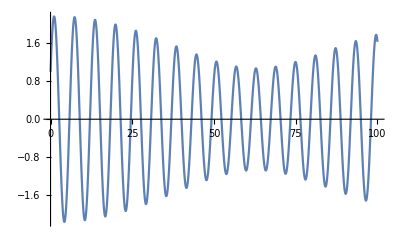

```mathematica
Plot[Cos[T]+.1((3 (ω^2-1) (.1)T Sin[T])/(4(ω^2-4))+(2ω -1)/(2ω(ω-2))Sin[T-ω T]+(1+2ω)/(2ω(ω+2))Sin[T+ ω T]),{T,0,100}]
```